```mathematica
SetDirectory[NotebookDirectory[]];<<ABCInterpolator.m
```

```mathematica
X1=Collect[n^(-p)Integrate[(t^(5/2)/n^5 - t^(15/2))t^(-p)(A + B t κ) E^(-C t κ),{t,0,Infinity}, GenerateConditions->False],n]
```

n^(-5-p) κ (C κ)^(-19/2+p) (A C^6 κ^5 Gamma[7/2-p]+B C^5 κ^5 Gamma[9/2-p])+n^-p κ (C κ)^(-19/2+p) (-A C Gamma[17/2-p]-B Gamma[19/2-p])

```mathematica
(n^(-5-p) κ (C κ)^(-19/2+p) (A C^6 κ^5 Gamma[7/2-p]+B C^5 κ^5 Gamma[9/2-p])+n^-p κ (C κ)^(-19/2+p) (-A C Gamma[17/2-p]-B Gamma[19/2-p]))//.n^(x_):> Zeta[-x-1]/Zeta[-x]
```

(κ (C κ)^(-19/2+p) (-A C Gamma[17/2-p]-B Gamma[19/2-p]) Zeta[-1+p])/Zeta[p]+(κ (C κ)^(-19/2+p) (A C^6 κ^5 Gamma[7/2-p]+B C^5 κ^5 Gamma[9/2-p]) Zeta[4+p])/Zeta[5+p]

```mathematica
I1 =FullSimplify[((κ (C κ)^(-19/2+p) (-A C Gamma[17/2-p]-B Gamma[19/2-p]) Zeta[-1+p])/(p Zeta[p]))/.{p->17/2 + q,κ->1 }]
```

(2 C^(-1+q) (-A C+B q) Gamma[-q] Zeta[15/2+q])/((17+2 q) Zeta[17/2+q])

```mathematica
I2 =FullSimplify[((κ (C κ)^(-19/2+p) (A C^6 κ^5 Gamma[7/2-p]+B C^5 κ^5 Gamma[9/2-p]) Zeta[4+p])/(p Zeta[5+p]))/.{p->19/2 -6+ q,κ->1 }]
```

(2 C^(-1+q) (A C-B q) Gamma[-q] Zeta[15/2+q])/((7+2 q) Zeta[17/2+q])

```mathematica
I1 + I2//FullSimplify
```

(20 C^(-1+q) (A C-B q) Gamma[-q] Zeta[15/2+q])/((119+48 q+4 q^2) Zeta[17/2+q])

```mathematica
Factor[(119+48 q+4 q^2)]
```

(7+2 q) (17+2 q)

```mathematica
((Gamma[-q] Zeta[15/2+q])/((7+2 q) (17+2 q) Zeta[17/2+q]))/.q->p
```

(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p])

```mathematica
F == 20 C^(-1+q) (A C-B q)
```

F==20 C^(-1+q) (A C-B q)

```mathematica
pts = FunctionPoles[{(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]),{ Abs[p] < 50}},p]
```

{{-97/2,1},{-93/2,1},{-89/2,1},{-85/2,1},{-81/2,1},{-77/2,1},{-73/2,1},{-69/2,1},{-65/2,1},{-61/2,1},{-57/2,1},{-53/2,1},{-49/2,1},{-45/2,1},{-41/2,1},{-37/2,1},{-33/2,1},{-29/2,1},{-25/2,1},{-21/2,1},{-17/2,1},{-13/2,1},{-7/2,1},{0,1},{1,1},{2,1},{3,1},{4,1},{5,1},{6,1},{7,1},{8,1},{9,1},{10,1},{11,1},{12,1},{13,1},{14,1},{15,1},{16,1},{17,1},{18,1},{19,1},{20,1},{21,1},{22,1},{23,1},{24,1},{25,1},{26,1},{27,1},{28,1},{29,1},{30,1},{31,1},{32,1},{33,1},{34,1},{35,1},{36,1},{37,1},{38,1},{39,1},{40,1},{41,1},{42,1},{43,1},{44,1},{45,1},{46,1},{47,1},{48,1},{49,1},{1/2 (-17+2 ZetaZero[-9]),1},{1/2 (-17+2 ZetaZero[-8]),1},{1/2 (-17+2 ZetaZero[-7]),1},{1/2 (-17+2 ZetaZero[-6]),1},{1/2 (-17+2 ZetaZero[-5]),1},{1/2 (-17+2 ZetaZero[-4]),1},{1/2 (-17+2 ZetaZero[-3]),1},{1/2 (-17+2 ZetaZero[-2]),1},{1/2 (-17+2 ZetaZero[-1]),1},{1/2 (-17+2 ZetaZero[1]),1},{1/2 (-17+2 ZetaZero[2]),1},{1/2 (-17+2 ZetaZero[3]),1},{1/2 (-17+2 ZetaZero[4]),1},{1/2 (-17+2 ZetaZero[5]),1},{1/2 (-17+2 ZetaZero[6]),1},{1/2 (-17+2 ZetaZero[7]),1},{1/2 (-17+2 ZetaZero[8]),1},{1/2 (-17+2 ZetaZero[9]),1}}

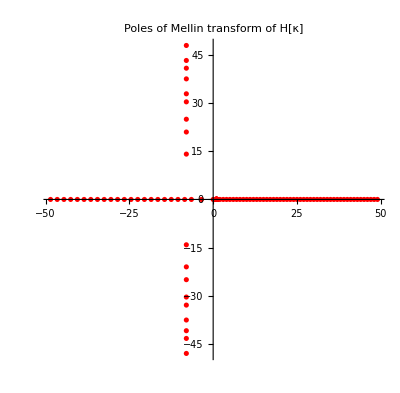

```mathematica
ComplexListPlot[pts, PlotStyle->{Red},PlotLabel->"Poles of Mellin transform of H[κ]"]
```

```mathematica
FunctionPoles[(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]),p]//TableForm
```

-17/2 | 1
-13/2 | 1
-7/2 | 1
ConditionalExpression[1/2 (-17-4 C[1]), C[1]∈ℤ&&C[1]≥1] | 1
ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1+2 C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1/2 (-17+2 ZetaZero[C[1]]), C[1]∈ℤ] | Indeterminate

```mathematica
{a,b,c} = ABC[0.3]
```

{1.14196,0.00305917,0.0601122}

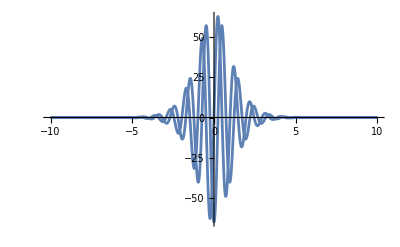

```mathematica
Plot[ReIm[((20 c (-a c+b q) Gamma[-q] Zeta[15/2+q])/((119+48 q+4 q^2) Zeta[17/2+q])(0.1 c)^q)/.q->-2+ I x],{x,-10,10}, PlotRange->All]
```

```mathematica
Residue[(20 C^(-1+q) (A C-B q) Gamma[-q] Zeta[15/2+q])/((119+48 q+4 q^2) Zeta[17/2+q]),{q,0}]
```

-(20 A Zeta[15/2])/(119 Zeta[17/2])

```mathematica
HIntegral[A_, B_, C_,κ_, dt_] := TimeConstrained[Re[NIntegrate[((20 C^(-1+q) (A C-B q) Gamma[-q] Zeta[15/2+q])/((119+48 q+4 q^2) Zeta[17/2+q])κ^q)/.q->-2+ I x,
{x,-Infinity,Infinity},PrecisionGoal->6, Method->"DoubleExponentialOscillatory"]]/(2 Pi),dt];
```

```mathematica
HIntegral[a,b,c,0.1,1]//Timing
```

{0.186039,0.191727}

```mathematica
{0.147472,0.19172736546406138}
```

{0.147472,0.191727}

```mathematica
{0.152756,0.19172736546406138}
```

{0.152756,0.191727}

```mathematica
HIntegral[a,b,c,100,1]//Timing
```

{0.040958,0.00644511}

```mathematica
HIntegral[a,b,c,1000,1]//Timing
```

{0.053351,2.71845×10^-6}

```mathematica
HH[κ_] :=
Block[{ tab,OKtab, interp, delta = (Δ2 - Δ1)/100},
tab =(*Parallel*)Table[
Block[{A,B,C, ZI} ,
{A,B,C}= ABC[Δ];
(*Print[{Δ,{A,B,C}}];*)
ZI = HIntegral[A,B,C ,κ,1];
(*Print[{Δ,ZI}];*)
{Δ,Log[ZI]}], {Δ,Δ1, Δ2, delta}];
OKtab = Select[tab,NumericQ[#[[2]]]&];
If[Length[OKtab] < 10, Return[None]];
interp = Interpolation[OKtab,InterpolationOrder->5];
NIntegrate[(1-Δ)Exp[interp[Δ]],{Δ,Δ1, Δ2}]
]
```

```mathematica
HH[0.5]
```

0.0363317

```mathematica
htable[k0_, k1_, M_] := 
ParallelTable[
Block[{k},
k = N[k0 (k1/k0)^(n/M )];
{k,HH[k]}]
,{n,0,M}];
```

```mathematica
htable[0.1,1,100]
```

{{0.1,0.0369082},{0.102329,0.0369048},{0.104713,0.0369013},{0.107152,0.0368978},{0.109648,0.0368942},{0.112202,0.0368904},{0.114815,0.0368866},{0.11749,0.0368828},{0.120226,0.0368788},{0.123027,0.0368747},{0.125893,0.0368706},{0.128825,0.0368663},{0.131826,0.036862},{0.134896,0.0368575},{0.138038,0.0368529},{0.141254,0.0368483},{0.144544,0.0368435},{0.147911,0.0368386},{0.151356,0.0368336},{0.154882,0.0368285},{0.158489,0.0368233},{0.162181,0.0368179},{0.165959,0.0368124},{0.169824,0.0368068},{0.17378,0.0368011},{0.177828,0.0367952},{0.18197,0.0367892},{0.186209,0.0367831},{0.190546,0.0367768},{0.194984,0.0367704},{0.199526,0.0367638},{0.204174,0.0367571},{0.20893,0.0367502},{0.213796,0.0367432},{0.218776,0.036736},{0.223872,0.0367286},{0.229087,0.0367211},{0.234423,0.0367134},{0.239883,0.0367055},{0.245471,0.0366974},{0.251189,0.0366891},{0.25704,0.0366807},{0.263027,0.036672},{0.269153,0.0366632},{0.275423,0.0366541},{0.281838,0.0366449},{0.288403,0.0366354},{0.295121,0.0366257},{0.301995,0.0366158},{0.30903,0.0366057},{0.316228,0.0365953},{0.323594,0.0365847},{0.331131,0.0365739},{0.338844,0.0365628},{0.346737,0.0365514},{0.354813,0.0365398},{0.363078,0.0365279},{0.371535,0.0365158},{0.380189,0.0365033},{0.389045,0.0364906},{0.398107,0.0364776},{0.40738,0.0364643},{0.416869,0.0364507},{0.42658,0.0364368},{0.436516,0.0364225},{0.446684,0.0364079},{0.457088,0.036393},{0.467735,0.0363778},{0.47863,0.0363622},{0.489779,0.0363463},{0.501187,0.03633},{0.512861,0.0363133},{0.524807,0.0362962},{0.537032,0.0362788},{0.549541,0.0362609},{0.562341,0.0362427},{0.57544,0.036224},{0.588844,0.0362049},{0.60256,0.0361854},{0.616595,0.0361654},{0.630957,0.036145},{0.645654,0.0361241},{0.660693,0.0361027},{0.676083,0.0360809},{0.691831,0.0360586},{0.707946,0.0360357},{0.724436,0.0360124},{0.74131,0.0359885},{0.758578,0.0359641},{0.776247,0.0359391},{0.794328,0.0359136},{0.812831,0.0358874},{0.831764,0.0358607},{0.851138,0.0358334},{0.870964,0.0358055},{0.891251,0.035777},{0.912011,0.0357478},{0.933254,0.035718},{0.954993,0.0356875},{0.977237,0.0356563},{1.,0.0356244}}

```mathematica
(*htab= htable[0.1,100,1000]*)
```

```mathematica
htab={{0.1,0.03690817607609459},{0.10069316688518043,0.03690716863614085},{0.10139113857366795,0.036906154242555625},{0.102093948370768,0.03690513284748546},{0.10280162981264736,0.03690410440276247},{0.1035142166679344,0.03690306885986018},{0.10423174293933042,0.0369020261700067},{0.10495424286523224,0.03690097628403232},{0.10568175092136585,0.036899919152412156},{0.10641430182243161,0.03689885472543311},{0.10715193052376065,0.03689778295290045},{0.10789467222298288,0.03689670378434977},{0.10864256236170655,0.036895617168976734},{0.1093956366272094,0.03689452305561852},{0.1101539309541415,0.03689342139278178},{0.1109174815262401,0.036892312128650386},{0.11168632477805612,0.03689119521104481},{0.11246049739669264,0.03689007058740829},{0.11324003632355571,0.03688893820486436},{0.11402497875611686,0.03688779801016705},{0.1148153621496883,0.036886649949757044},{0.11561122421920988,0.03688549396962191},{0.11641260294104915,0.03688433001548312},{0.11721953655481306,0.03688315803261297},{0.11803206356517298,0.03688197796596577},{0.11885022274370186,0.03688078976010544},{0.11967405313072435,0.03687959335917684},{0.12050359403717975,0.036878388707054975},{0.12133888504649773,0.036877175747068856},{0.12217996601648717,0.03687595442230241},{0.12302687708123816,0.03687472467537014},{0.12387965865303692,0.03687348644849989},{0.1247383514242943,0.0368722396835492},{0.1256029963694875,0.036870984321992616},{0.12647363474711512,0.03686972030482933},{0.12735030810166617,0.036868447572721647},{0.12823305826560213,0.036867166065870184},{0.12912192736135342,0.03686587572413569},{0.13001695780332903,0.03686457648690533},{0.1309181922999407,0.036863268293161854},{0.1318256738556407,0.03686195108149731},{0.13273944577297395,0.03686062479007177},{0.13365955165464424,0.03685928935661844},{0.13458603540559483,0.03685794471843841},{0.1355189412351036,0.036856590812439936},{0.13645831365889247,0.036855227575063085},{0.13740419750125152,0.03685385494235669},{0.1383566378971781,0.036852472849912145},{0.13931568029453031,0.036851081232896314},{0.14028137045619582,0.036849680026036724},{0.14125375446227545,0.03684826916362021},{0.142232878712282,0.036846848579494274},{0.14321878992735435,0.036845418207064176},{0.14421153515248689,0.03684397797929459},{0.14521116175877422,0.03684252782867599},{0.14621771744567183,0.03684106768726775},{0.14723125024327188,0.03683959748667031},{0.14825180851459538,0.03683811715802336},{0.14927944095789963,0.03683662663200757},{0.15031419660900225,0.03683512583883462},{0.15135612484362082,0.03683361470823135},{0.15240527537972914,0.03683209316948133},{0.15346169827992945,0.036830561151390884},{0.15452544395384138,0.03682901858226058},{0.15559656316050746,0.03682746538992117},{0.1566751070108149,0.03682590150174783},{0.15776112696993488,0.03682432684456131},{0.1588546748597779,0.03682274134475112},{0.1599558028614669,0.03682114492816624},{0.16106456351782705,0.03681953752018478},{0.162181009735893,0.03681791904565349},{0.16330519478943345,0.03681628942893622},{0.16443717232149316,0.03681464859386219},{0.1655769963469528,0.036812996463760926},{0.1667247212551063,0.03681133296142394},{0.16788040181225605,0.03680965800915282},{0.16904409316432642,0.036807971528684695},{0.1702158508394951,0.036806273441261916},{0.17139573075084255,0.03680456366756788},{0.17258378919902037,0.03680284212776895},{0.17378008287493757,0.03680110874146561},{0.17498466886246572,0.036799363427744536},{0.17619760464116294,0.03679760610512757},{0.1774189480890166,0.036795836691601566},{0.1786487574852051,0.03679405510458024},{0.1798870915128788,0.03679226126094},{0.18113400926196024,0.03679045507699313},{0.18238957023196378,0.03678863646849324},{0.18365383433483465,0.036786805350607785},{0.18492686189780783,0.036784961637953584},{0.18620871366628677,0.03678310524458543},{0.18749945080674188,0.036781236083953624},{0.18879913490962935,0.03677935406894991},{0.19010782799233,0.03677745911187052},{0.19142559250210858,0.03677555112443343},{0.1927524913190936,0.03677363001776133},{0.19408858775927784,0.036771695702389195},{0.19543394557753946,0.036769748088253756},{0.1967886289706845,0.03676778708467827},{0.19815270258050985,0.036765812600380594},{0.19952623149688797,0.036763824543508315},{0.20090928126087282,0.036761822821530496},{0.20230191786782714,0.03675980734134956},{0.20370420777057185,0.03675777800922363},{0.20511621788255652,0.03675573473078821},{0.20653801558105292,0.036753677411045925},{0.20796966871036957,0.036751605954380644},{0.20941124558508928,0.036749520264511476},{0.21086281499332893,0.036747420244528504},{0.21232444620002197,0.0367453057968844},{0.21379620895022322,0.036743176823356496},{0.2152781734724373,0.03674103322507734},{0.2167704104819695,0.03673887490252548},{0.21827299118430019,0.03673670175549721},{0.21978598727848253,0.03673451368313731},{0.22130947096056378,0.03673231058389768},{0.2228435149270304,0.036730092355572404},{0.22438819237827665,0.0367278588952496},{0.22594357702209777,0.03672561009934587},{0.22750974307720706,0.03672334586358639},{0.22908676527677732,0.03672106608299011},{0.2306747188720069,0.036718770651879375},{0.2322736796357107,0.03671645946387097},{0.23388372386593548,0.036714132411876085},{0.23550492838960096,0.03671178938808804},{0.23713737056616552,0.03670943028398513},{0.23878112829131776,0.036707054990320724},{0.24043628000069336,0.03670466339712211},{0.24210290467361784,0.03670225539367708},{0.24378108183687527,0.036699830868555085},{0.24547089156850307,0.036697389709566666},{0.24717241450161304,0.03669493180379046},{0.24888573182823912,0.036692457037549926},{0.2506109253032114,0.03668996529641239},{0.25234807724805747,0.036687456465189706},{0.25409727055493053,0.036684930427931556},{0.2558585886905646,0.036682387067917384},{0.25763211570025757,0.03667982626764752},{0.2594179362118815,0.03667724790885886},{0.26121613543992067,0.03667465187249548},{0.26302679918953825,0.03667203803871414},{0.26485001386067003,0.03666940628688238},{0.266685866452148,0.0366667564955693},{0.26853444456585074,0.03666408854253686},{0.2703958364108844,0.03666140230475095},{0.2722701308077912,0.03665869765834743},{0.27415741719278824,0.036655974478660903},{0.2760577856220346,0.036653232640192365},{0.2779713267759289,0.036650472016620465},{0.27989813196343627,0.036647692480779676},{0.28183829312644537,0.03664489390467623},{0.2837919028441556,0.036642076159466776},{0.2857590543374947,0.036639239115460076},{0.28773984147356696,0.03663638264210529},{0.2897343587701323,0.03663350660799559},{0.2917427014001167,0.0366306108808551},{0.2937649651961531,0.03662769532753581},{0.2958012466551546,0.03662475981401473},{0.297851642942919,0.03662180420537892},{0.29991625189876514,0.036618828365842},{0.30199517204020165,0.03661583215870755},{0.3040885025676279,0.03661281544638735},{0.30619634336906776,0.03660977809038795},{0.3083187950249355,0.03660671995130645},{0.3104559588128356,0.03660364088881688},{0.3126079367123955,0.036600540761682385},{0.31477483141013163,0.03659741942772987},{0.31695674630434917,0.036594276743857256},{0.31915378551007617,0.0365911125660244},{0.3213660538640318,0.0365879267492421},{0.32359365692962827,0.03658471915896758},{0.32583670100200884,0.036581489622909136},{0.328095293113119,0.03657823801947328},{0.3303695410368148,0.03657496417031816},{0.3326595532940045,0.036571667967286905},{0.3349654391578276,0.03656834922311162},{0.33728730865886886,0.03656500782364514},{0.3396252725904084,0.03656164365669593},{0.3419794425137088,0.03655825640041183},{0.3443499307633385,0.03655484604478984},{0.34673685045253166,0.03655141242923162},{0.34914031547858615,0.036547955362688345},{0.35156044052829816,0.03654447462483425},{0.3539973410834347,0.03654097015183337},{0.35645113342624424,0.03653744172422132},{0.3589219346450052,0.03653388918662618},{0.36140986263961333,0.036530312341508525},{0.36391503612720716,0.036526711118396324},{0.3664375746478333,0.036523085275935674},{0.36897759857015033,0.036519434711736576},{0.37153522909717257,0.03651575920185397},{0.37411058827205335,0.03651205862635325},{0.3767037989839089,0.03650833278747321},{0.37931498497368193,0.0365045815249351},{0.3819442708400466,0.03650080467762598},{0.3845917820453536,0.03649700205785825},{0.38725764492161724,0.036493173517957535},{0.38994198667654345,0.036489318861529986},{0.3926449353995999,0.03648543792083277},{0.39536662006812795,0.03648153053982484},{0.3981071705534973,0.03647759652750898},{0.40086671762730286,0.03647363569340051},{0.403645392967605,0.036469647877694356},{0.40644332916521286,0.03646563290305585},{0.4092606597300108,0.03646159056929062},{0.41209751909733017,0.03645752069972486},{0.4149540426343629,0.03645342312291243},{0.4178303666466218,0.0364492976416661},{0.420726628384444,0.03644514406626318},{0.4236429660495411,0.03644096222176673},{0.4265795188015926,0.03643675191289648},{0.42953642676488724,0.036432512940710544},{0.43251383103500873,0.036428245126451396},{0.4355118736855686,0.036423948277808246},{0.4385306977749857,0.03641962218526483},{0.44157044735331247,0.03641526666110322},{0.4446312674691087,0.03641088152073338},{0.4477133041763625,0.036406466551227507},{0.45081670454146017,0.03640202154716848},{0.4539416166502032,0.036397546325166584},{0.4570881896148751,0.036393040681270986},{0.4602565735813561,0.03638850439694724},{0.46344691973628804,0.036383937276151676},{0.46665938031428866,0.036379339122116466},{0.46989410860521547,0.036374709715629484},{0.4731512589614806,0.036370048846700705},{0.47643098680541573,0.03636535631625765},{0.4797334486366892,0.03636063190726996},{0.4830588020397727,0.03635587540126175},{0.4864072056914617,0.03635108659445898},{0.48977881936844625,0.03634626527052574},{0.493173803954936,0.03634141120272532},{0.4965923214503361,0.036336524181674636},{0.5000345349769786,0.03633160399529401},{0.5035006087879048,0.0363266504103384},{0.5069907082747043,0.03632166320418442},{0.5105049999754062,0.03631664216766796},{0.514043651582426,0.036311587070957704},{0.5176068319505677,0.03630649767720109},{0.5211947111050804,0.03630137376927456},{0.5248074602497725,0.03629621512417759},{0.5284452517751804,0.03629102150048601},{0.5321082592667942,0.036285792667628776},{0.5357966575133416,0.03628052840225684},{0.5395106225151277,0.03627522846452065},{0.5432503314924332,0.0362698926146042},{0.5470159628939716,0.03626452062362949},{0.5508076964054034,0.03625911225125379},{0.5546257129579107,0.036253667250394396},{0.5584701947368308,0.036248185386783434},{0.5623413251903492,0.03624266642064752},{0.5662392890382533,0.03623711009725403},{0.5701642722807475,0.03623151617257047},{0.5741164622073276,0.03622588440889373},{0.5780960474057182,0.036220214549953514},{0.5821032177708715,0.03621450633817248},{0.5861381645140288,0.03620875953140115},{0.5902010801718444,0.036202973877811385},{0.5942921586155727,0.03619714911158029},{0.5984115950603197,0.03619128497831502},{0.6025595860743578,0.036185381226754715},{0.6067363295885055,0.036179437590253355},{0.6109420249055721,0.03617345380367579},{0.6151768727098683,0.03616742961014308},{0.6194410750767815,0.03616136474205908},{0.6237348354824194,0.036155258927082795},{0.628058358813318,0.036149111902190764},{0.6324118513762196,0.03614292339804489},{0.6367955209079159,0.0361366931349818},{0.6412095765851618,0.036130420842420644},{0.6456542290346556,0.036124106251068606},{0.6501296903430909,0.036117749076317596},{0.6546361740672751,0.03611134903570322},{0.6591738952443215,0.03610490585729523},{0.6637430704019089,0.03609841925764921},{0.6683439175686148,0.03609188894400334},{0.6729766562843179,0.03608531463457106},{0.6776415076106752,0.036078696046916804},{0.6823386941416698,0.03607203288491817},{0.6870684400142323,0.03606532485563673},{0.6918309709189366,0.036058571672172454},{0.6966265141107688,0.03605177303731204},{0.7014552984199711,0.03604492865042017},{0.7063175542629619,0.03603803821779242},{0.711213513653329,0.03603110143939979},{0.716143410212902,0.036024118007849555},{0.7211074791828995,0.03601708762273328},{0.7261059574351547,0.03601000998204335},{0.7311390834834174,0.03600288477197944},{0.7362070974947361,0.035995711682401926},{0.7413102413009174,0.03598849040921309},{0.7464487584100664,0.03598122063678114},{0.7516228940182055,0.035973902044311515},{0.7568328950209744,0.03596653432037183},{0.762079010025412,0.03595911714968191},{0.7673614893618189,0.03595165020546259},{0.7726805850957024,0.03594413316530947},{0.778036551039804,0.035936565710421954},{0.7834296427662117,0.035928947511867336},{0.7888601176185543,0.03592127823846854},{0.7943282347242815,0.035913557564315954},{0.7998342550070284,0.03590578515721208},{0.8053784411990667,0.03589796067927755},{0.8109610578538407,0.035890083797678},{0.8165823713585925,0.03588215417655535},{0.8222426499470711,0.03587417147111714},{0.8279421637123342,0.03586613534014499},{0.8336811846196343,0.03585804544473187},{0.8394599865193975,0.035849901435425414},{0.84527884516029,0.035841702960495665},{0.8511380382023765,0.03583344967507176},{0.8570378452303697,0.03582514122818381},{0.8629785477669704,0.035816777259875865},{0.8689604292863019,0.0358083574150247},{0.8749837752274362,0.035799881339531235},{0.8810488730080142,0.03579134866954437},{0.8871560120379609,0.035782759040173},{0.8933054837332954,0.035774112090387326},{0.8994975815300352,0.03576540745265077},{0.9057326008982001,0.03575664475468095},{0.9120108393559099,0.03574782362770558},{0.918332596483581,0.03573894369926861},{0.9246981739382227,0.03573000458995036},{0.9311078754678305,0.03572100592306985},{0.9375620069258803,0.03571194732172275},{0.9440608762859235,0.035702828400049645},{0.9506047936562816,0.03569364877161311},{0.9571940712948446,0.0356844080541812},{0.9638290236239707,0.0356751058584037},{0.9705099672454898,0.035665741788504866},{0.9772372209558109,0.03565631545322332},{0.9840111057611338,0.03564682645992604},{0.9908319448927678,0.03563727440703209},{0.9977000638225535,0.03562765889304073},{1.0046157902783954,0.03561797951891671},{1.0115794542598988,0.03560823587885884},{1.018591388054117,0.03559842756314622},{1.0256519262514077,0.03558855416459148},{1.0327614057613976,0.03557861527203622},{1.0399201658290593,0.03556861046865119},{1.0471285480508998,0.03555853933943214},{1.054386896391259,0.035548401467716685},{1.0616955571987248,0.035538196429499055},{1.0690548792226582,0.03552792380083556},{1.0764652136298347,0.03551758315957567},{1.0839269140212033,0.03550717407637113},{1.0914403364487564,0.035496696117591355},{1.0990058394325208,0.03548614885312437},{1.1066237839776663,0.035475531849588564},{1.1142945335917298,0.035464844665885335},{1.1220184543019633,0.03545408686179288},{1.1297959146727976,0.0354432579980359},{1.1376272858234306,0.03543235762843038},{1.1455129414455356,0.03542138530371363},{1.153453257821092,0.03541034057637237},{1.1614486138403428,0.03539922299455915},{1.1694993910198708,0.03538803210145342},{1.1776059735208073,0.03537676744121385},{1.18576874816716,0.03536542855552629},{1.193988104464273,0.035354014979945156},{1.2022644346174127,0.03534252624998291},{1.2105981335504823,0.03533096190105171},{1.2189895989248665,0.035319321461849386},{1.2274392311584073,0.03530760445824845},{1.2359474334445104,0.03529581041823773},{1.2445146117713852,0.035283938865268094},{1.253141174941416,0.03527198931645813},{1.2618275345906707,0.03525996129003113},{1.2705741052085417,0.03524785430351738},{1.2793813041575248,0.03523566786759909},{1.288249551693134,0.03522340149067834},{1.297179270983956,0.03521105468209848},{1.3061708881318417,0.035198626946430396},{1.3152248321922384,0.03518611778376411},{1.3243415351946648,0.03517352669457125},{1.333521432163324,0.03516085317639456},{1.342764961137864,0.03514809672147074},{1.3520725631942774,0.03513525682161387},{1.36144468246595,0.03512233296727736},{1.3708817661648538,0.035109324642917564},{1.380384264602885,0.03509623133093915},{1.3899526312133534,0.03508305251440482},{1.3995873225726183,0.03506978767126009},{1.409288798421875,0.0350564362744763},{1.4190575216890924,0.0350429977979058},{1.428893958511103,0.03502947171328413},{1.4387985782558457,0.03501585748595571},{1.4487718535447618,0.035002154579735656},{1.4588142602753487,0.034988362458553135},{1.468926277643867,0.034974480581236436},{1.4791083881682077,0.03496050840267835},{1.4893610777109156,0.03494644537776696},{1.4996848355023737,0.03493229095811502},{1.5100801541641486,0.03491804459055563},{1.5205475297324957,0.03490370572112688},{1.5310874616820305,0.034889273793785605},{1.5417004529495597,0.03487474824720648},{1.5523870099580825,0.03486012851830879},{1.5631476426409545,0.03484541404345978},{1.5739828644662197,0.03483060425389878},{1.5848931924611138,0.0348156985770325},{1.595879147236733,0.034800696440591965},{1.6069412530128777,0.034785597269148254},{1.6180800376430662,0.03477040048159014},{1.629296032639723,0.03475510549576137},{1.6405897731995396,0.034739711728683245},{1.6519617982290153,0.034724218592102674},{1.6634126503701692,0.03470862549441369},{1.6749428760264373,0.034692931843650014},{1.6865530253887409,0.03467713704422171},{1.6982436524617441,0.034661240496118934},{1.7100153150902875,0.034645241598274736},{1.721868574986007,0.034629139747138035},{1.733803997754138,0.034612934334417596},{1.7458221529205038,0.034596624750053845},{1.7579236139586927,0.034580210382533234},{1.770108958317421,0.034563690615467976},{1.7823787674480895,0.03454706482938047},{1.7947336268325262,0.03453033240437231},{1.807174126010927,0.034513492716733096},{1.8197008586099834,0.034496545137880454},{1.8323144223712113,0.03447948903835523},{1.8450154191794734,0.03446232378696139},{1.8578044550916983,0.034445048747310775},{1.8706821403658005,0.034427663280270394},{1.8836490894898004,0.03441016674596187},{1.8967059212111463,0.0343925585005744},{1.909853258566238,0.034374837896234564},{1.9230917289101583,0.03435700428387368},{1.9364219639466071,0.034339057011682654},{1.9498445997580456,0.03432099542349965},{1.9633602768360465,0.03430281886131646},{1.9769696401118608,0.03428452666513739},{1.990673338987187,0.03426611817049544},{2.004472027365161,0.03424759271029177},{2.018366363681561,0.034228949616353775},{2.0323570109362215,0.03421018821651072},{2.046444636724674,0.03419130783455873},{2.06062991327,0.0341723077933804},{2.07491351745491,0.034153187413419564},{2.0892961308540396,0.03413394601029967},{2.1037784397664754,0.03411458289746846},{2.118361135248502,0.034095097387229115},{2.1330449131465765,0.03407548878780082},{2.1478304741305343,0.03405575640382133},{2.1627185237270203,0.03403589953871845},{2.177709772353159,0.03401591749303497},{2.192804935350449,0.03399580956332605},{2.2080047330189,0.033975575044340615},{2.2233098906514033,0.033955213228634824},{2.23872113856834,0.03393472340474525},{2.2542392121524295,0.033914104858867394},{2.2698648518838223,0.03389335687567296},{2.2855988033754304,0.03387247873598231},{2.301441817408509,0.03385146971731764},{2.3173946499684788,0.03383032909612705},{2.3334580622810033,0.033809056146009236},{2.3496328208483077,0.03378765013632521},{2.365919697485759,0.033766110334719414},{2.382319469358691,0.03374443600731829},{2.398832919019491,0.033722626416236745},{2.415460834444941,0.03370068082059658},{2.432204009073816,0.03367859847833735},{2.4490632418447458,0.03365637864443344},{2.46603933723434,0.03363402057026},{2.483133105295571,0.03361152350553643},{2.500345361696432,0.03358888669776416},{2.517676927758856,0.03356610939084674},{2.5351286304979084,0.033543190826577134},{2.5527013026612466,0.03352013024502223},{2.5703957827688635,0.03349692688275119},{2.5882129151530915,0.033473579973648165},{2.6061535499988953,0.03345008875038357},{2.6242185433844414,0.03342645244270506},{2.642408757321946,0.03340267027683905},{2.6607250597988092,0.03337874147764761},{2.6791683248190314,0.03335466526821583},{2.69773943244492,0.033330440867942894},{2.7164392688390824,0.03330606749389542},{2.735268726306712,0.03328154436201714},{2.7542287033381663,0.03325687068534611},{2.7733201046518405,0.033232045673848944},{2.792543841237338,0.03320706853614012},{2.8119008303989403,0.03318193847875951},{2.831391995799379,0.03315665470513777},{2.851018267503909,0.03313121641694177},{2.870780582024691,0.03310562281421064},{2.8906798823654754,0.033079873094012474},{2.9107171180666054,0.03305396645130801},{2.9308932452503207,0.03302790207987668},{2.9512092266663856,0.03300167917085175},{2.9716660317380263,0.03297529691265968},{2.992264636608189,0.032948754492706914},{3.0130060241861214,0.032922051096619095},{3.0338911841942706,0.03289518590695477},{3.0549211132155136,0.032868158104682924},{3.0760968147407084,0.032840966869819056},{3.0974192992165803,0.03281361137978417},{3.118889584093937,0.032786090809666095},{3.1405086938762174,0.03275840433366091},{3.1622776601683795,0.03273055112419733},{3.1841975217261247,0.03270253035121554},{3.2062693245054663,0.03267434118342082},{3.2284941217126355,0.0326459827882484},{3.250872973854344,0.03261745433082223},{3.2734069487883826,0.03258875497478876},{3.296097121774578,0.03255988388289323},{3.3189445755261042,0.03253084021581176},{3.3419504002611427,0.032501623132398794},{3.3651156937549076,0.032472231790914484},{3.3884415613920256,0.03244266534814712},{3.4119291162192855,0.03241292295868044},{3.4355794789987466,0.03238300377629795},{3.4593937782612194,0.03235290695414226},{3.483373150360118,0.03232263164334564},{3.507518739525681,0.03229217699362643},{3.53183169791957,0.032261542154396236},{3.556313185689854,0.03223072627378695},{3.580964371026361,0.032199728498251604},{3.605786430216425,0.03216854797374441},{3.6307805477010144,0.03213718384553891},{3.65594791613125,0.03210563525741185},{3.681289736425315,0.03207390135244488},{3.706807217825761,0.032041981273389315},{3.7325015779572066,0.032009874161758295},{3.7583740428844425,0.03197757915821935},{3.784425847170934,0.03194509540345273},{3.8106582339377315,0.031912422037322266},{3.8370724549227884,0.031879558198572966},{3.8636697705406924,0.031846503026039565},{3.890451449942807,0.03181325565848001},{3.9174187710778323,0.03177981523356272},{3.9445730207527854,0.031746180888674015},{3.9719154946944037,0.031712351761669505},{3.999447497610976,0.031678326989896866},{4.027170343254592,0.03164410571011641},{4.055085354483839,0.031609687059576584},{4.083193863326922,0.031575070175692756},{4.111497211045224,0.0315402541954318},{4.139996748197305,0.03150523825610553},{4.1686938347033555,0.03147002149559752},{4.197589839910076,0.03143460305165386},{4.226686142656031,0.03139898206233404},{4.255984131337432,0.03136315766661774},{4.285485203974397,0.03132712900370838},{4.315190768277653,0.03129089521301959},{4.345102241715717,0.031254455435141416},{4.375221051582522,0.031217808811501106},{4.405548635065535,0.03118095448371297},{4.436086439314327,0.03114389159445994},{4.466835921509633,0.03110661928791307},{4.497798548932881,0.031069136708849955},{4.52897579903621,0.031031443002859805},{4.560369159512963,0.030993537317263592},{4.591980128368688,0.030955418800678487},{4.623810213992605,0.03091708660261459},{4.655860935229591,0.03087853987427278},{4.688133821452654,0.030839777768658556},{4.7206304126359075,0.03080079944001956},{4.753352259428055,0.030761604044325982},{4.786300923226385,0.03072219073971831},{4.819477976251275,0.030682558685957338},{4.852885001621213,0.03064270704458036},{4.886523593428334,0.030602634979643564},{4.920395356814508,0.030562341657338846},{4.9545019080479005,0.030521826245660535},{4.988844874600121,0.030481087915253204},{5.02342589522387,0.030440125839574176},{5.058246620031139,0.03039893919419279},{5.093308710571953,0.030357527157214754},{5.128613839913648,0.030315888910008124},{5.164163692720709,0.03027402363670662},{5.199959965335158,0.030231930524032016},{5.236004365857501,0.030189608762083035},{5.272298614228227,0.030147057544341542},{5.308844442309883,0.030104276067237454},{5.345643593969715,0.030061263530665107},{5.382697825162882,0.03001801913833211},{5.420008904016237,0.02997454209733639},{5.457578610912709,0.029930831618420264},{5.495408738576245,0.02988688691654776},{5.5335010921573655,0.029842707210561897},{5.571857489319298,0.029798291723093232},{5.610479760324704,0.029753639681310787},{5.649369748123025,0.029708750316919618},{5.688529308438413,0.029663622865682512},{5.727960309858291,0.029618256567977466},{5.767664633922506,0.029572650669317246},{5.80764417521312,0.029526804419861327},{5.847900841444806,0.02948071707445985},{5.888436553555889,0.02943438789339771},{5.929253245799997,0.02938781614230425},{5.970352865838368,0.02934100109185246},{6.01173737483278,0.029293942018319134},{6.053408747539135,0.029246638203858182},{6.09536897240169,0.02919908893617368},{6.137620051647941,0.02915129350883556},{6.180164001384158,0.029103251221749362},{6.223002851691594,0.029054961380886986},{6.266138646723353,0.029006423298357443},{6.309573444801932,0.028957636293042877},{6.353309318517436,0.028908599690519843},{6.39734835482648,0.02885931282280108},{6.441692655151773,0.028809775028945092},{6.486344335482383,0.02875998565539364},{6.531305526474724,0.028709944055559863},{6.576578373554205,0.02865964959006616},{6.62216503701762,0.02860910162740282},{6.668067692136221,0.028558299543765774},{6.714288529259523,0.02850724272290769},{6.760829753919818,0.028455930556735506},{6.807693586937415,0.02840436244551061},{6.854882264526616,0.028352537797602217},{6.902398038402419,0.028300456029858735},{6.950243175887969,0.02824811656801348},{6.998419960022734,0.028195518846492244},{7.046930689671469,0.02814266230859828},{7.095777679633888,0.028089546407029358},{7.144963260755133,0.028036170603807167},{7.194489780036995,0.027982534370213207},{7.244359600749902,0.027928637187376794},{7.2945751025456875,0.027874478546482097},{7.345138681571149,0.02782005794848313},{7.396052750582378,0.027765374904479553},{7.44731973905989,0.02771042893626321},{7.498942093324558,0.027655219576129007},{7.550922276654339,0.027599746366881027},{7.6032627694018196,0.02754400886245024},{7.655966069112563,0.02748800662801745},{7.709034690644301,0.02743173923985335},{7.762471166286918,0.027375206285738352},{7.816278045883298,0.027318407365330612},{7.870457896950987,0.027261342090029304},{7.925013304804718,0.027204010083216757},{7.9799468726797675,0.027146410980744235},{8.035261221856173,0.02708854443085948},{8.090958991783824,0.027030410094277434},{8.147042840208398,0.02697200764473579},{8.203515443298183,0.026913336769116687},{8.260379495771788,0.026854397167300082},{8.31763771102671,0.026795188552629867},{8.375292821268827,0.026735710652340625},{8.433347577642754,0.02667596320737694},{8.491804750363139,0.026615945972563372},{8.550667128846834,0.02655565871719241},{8.609937521846009,0.026495101225083317},{8.66961875758217,0.026434273294510004},{8.729713683881117,0.02637317473868337},{8.790225168308845,0.02631180538606135},{8.851156098308357,0.02625016508026156},{8.912509381337456,0.026188253680365932},{8.974287945007488,0.026126071061349215},{9.036494737223016,0.026063617114056255},{9.099132726322518,0.02600089174536235},{9.162204901219999,0.02593789487867779},{9.225714271547634,0.025874626454033853},{9.289663867799366,0.02581108642806523},{9.354056741475521,0.025747274774509478},{9.418895965228415,0.025683191484525587},{9.484184633008974,0.025618836566565356},{9.549925860214362,0.025554210046664454},{9.61612278383665,0.02548931196897742},{9.682778562612494,0.025424142395781356},{9.749896377173872,0.025358701407506533},{9.817479430199846,0.02529298910325395},{9.885530946569391,0.025227005601044666},{9.954054173515273,0.025160751037769016},{10.023052380779,0.025094225569541977},{10.092528860766848,0.025027429372096552},{10.16248692870696,0.0249603626407849},{10.232929922807545,0.024893025590797046},{10.303861204416165,0.024825418457617272},{10.37528415818013,0.02475754149709855},{10.447202192208003,0.024689394985543508},{10.519618738232232,0.02462097922019492},{10.592537251772892,0.02455229451946896},{10.665961212302582,0.02448334122289568},{10.739894123412451,0.024414119691494478},{10.814339512979384,0.02434463030822728},{10.88930093333434,0.024274873477968754},{10.964781961431854,0.024204849627639174},{11.040786199020737,0.02413455920672733},{11.117317272815917,0.024064002687465957},{11.19437883467152,0.02399318056481689},{11.271974561755108,0.023922093356869973},{11.350108156723156,0.023850741605191645},{11.42878334789772,0.0237791258748296},{11.508003889444362,0.02370724675456825},{11.587773561551257,0.02363510485734308},{11.668096170609623,0.02356270082030525},{11.748975549395292,0.02349003530496267},{11.830415557251644,0.023417108997634842},{11.912420080273744,0.023343922609618258},{11.994993031493784,0.023270476877189864},{12.0781383510678,0.023196772562019196},{12.161860006463677,0.023122810451522403},{12.246161992650483,0.023048591358813136},{12.331048332289086,0.02297411612291936},{12.416523075924108,0.022899385609273192},{12.502590302177198,0.02282440070980081},{12.58925411794167,0.02274916234294354},{12.676518658578452,0.022673671454085602},{12.764388088113435,0.02259792901583446},{12.852866599436153,0.022521936028006406},{12.941958414499858,0.022445693517905672},{13.03166778452299,0.022369202540693318},{13.12199899019203,0.02229246417942179},{13.212956341865748,0.022215479545198542},{13.304544179780908,0.022138249777590623},{13.396766874259349,0.02206077604472472},{13.489628825916533,0.02198305954332737},{13.583134465871538,0.021905101499133512},{13.677288255958487,0.021826903167132292},{13.772094688939461,0.021748465831499496},{13.867558288718882,0.021669790805872266},{13.963683610559375,0.021590879433770825},{14.060475241299137,0.021511733088587816},{14.157937799570815,0.021432353173638154},{14.25607593602188,0.021352741122592812},{14.354894333536558,0.021272898399651838},{14.454397707459274,0.021192826499478144},{14.554590805819657,0.021112526947487907},{14.655478409559116,0.02103200130015325},{14.757065332758945,0.02095125114496453},{14.859356422870068,0.020870278100596416},{14.962356560944333,0.02078908381727405},{15.066070661867418,0.020707669976795823},{15.170503674593366,0.020626038292576563},{15.275660582380723,0.02054419051003184},{15.381546403030345,0.020462128406660427},{15.488166189124811,0.020379853791868286},{15.595525028269535,0.0202973685073198},{15.703628043335522,0.02021467442744024},{15.812480392703831,0.0201317734590937},{15.9220872705117,0.020048667541522992},{16.032453906900415,0.019965358646945174},{16.143585568264864,0.019881848780989503},{16.25548755750484,0.019798139980849516},{16.368165214278086,0.019714234318423472},{16.48162391525508,0.019630133898043127},{16.595869074375607,0.01954584085749993},{16.710906143107078,0.019461357367810714},{16.82674061070467,0.019376685633597065},{16.943378004473285,0.019291827892931036},{17.060823890031237,0.019206786417642976},{17.17908387157588,0.019121563513105122},{17.298163592151017,0.019036161316128442},{17.41806873391614,0.018950582807249036},{17.538805018417612,0.018864829785791407},{17.660378206861644,0.018778904894960882},{17.78279410038923,0.01869281060936356},{17.906058540352944,0.01860654943765382},{18.03017740859569,0.018520123922633535},{18.155156627731355,0.018433536640686383},{18.281002161427427,0.01834679017155047},{18.40772001468956,0.01825988725292858},{18.535316234148116,0.018172830470435157},{18.6637969083467,0.01808562256776736},{18.793168168032686,0.01799826629157624},{18.923436186449756,0.017910764422547548},{19.054607179632473,0.017823119775216514},{19.186687406702898,0.017735335198019758},{19.31968317016924,0.017647413573297292},{19.45360081622663,0.01755935781712474},{19.5884467350599,0.01747117087930386},{19.72422736114854,0.01738285574337526},{19.860949173573715,0.017294415508279076},{19.998618696327444,0.017205852978959924},{20.137242498623888,0.017117171484970235},{20.276827195212825,0.01702837408693333},{20.417379446695296,0.016939463859815138},{20.55890595984142,0.016850444062598925},{20.701413487910425,0.01676131788665061},{20.844908830972894,0.016672088426382636},{20.989398836235246,0.01658275942833096},{21.134890398366473,0.01649333361447703},{21.281390459827122,0.01640381485025397},{21.428906011200592,0.016314206190344377},{21.57744409152667,0.016224511114212286},{21.72701178863745,0.016134733084350438},{21.87761623949553,0.01604487557503343},{22.02926463053457,0.015954942091913612},{22.181964198002195,0.01586493617183744},{22.335722228305322,0.015774861348497905},{22.49054605835782,0.01568472132242751},{22.646443075930605,0.015594519620356774},{22.803420720004187,0.015504259935373034},{22.96148648112363,0.015413945956365246},{23.120647901755955,0.015323581401857113},{23.280912576650085,0.015233170048680291},{23.44228815319923,0.015142715586860001},{23.60478233180578,0.015052221908797372},{23.768402866248774,0.014961692819526166},{23.933157564053882,0.014871132240265546},{24.099054286865957,0.01478054388314054},{24.266100950824164,0.01468993184279743},{24.434305526939724,0.014599300004147234},{24.60367604147628,0.014508652337836868},{24.774220576332866,0.014417992840650007},{24.945947269429556,0.014327325530942016},{25.11886431509581,0.01423665446998778},{25.292979964461455,0.014145983717638923},{25.46830252585042,0.01405531746870724},{25.64484036517718,0.013964659566798536},{25.822601906345973,0.01387401443545745},{26.001595631652727,0.01378338615056069},{26.18183008218986,0.01369277890343576},{26.36331385825381,0.013602196837493499},{26.546055619755403,0.01351164439829835},{26.73006408663312,0.01342112563200988},{26.91534803926917,0.013330644885897558},{27.10191631890844,0.013240206457260933},{27.289777828080418,0.013149814663029074},{27.47894153102396,0.013059473839194383},{27.669416454115108,0.01296918834021787},{27.861211686297697,0.012878962538474625},{28.054336379517128,0.012788800823675438},{28.248799749157065,0.012698707602232543},{28.444611074479152,0.012608687307303126},{28.641779699065797,0.012518744344980863},{28.84031503126605,0.012428883200043959},{29.040226544644497,0.012339108328894302},{29.241523778433347,0.012249424212139159},{29.444216337987605,0.012159835347288851},{29.64831389524342,0.012070346227957465},{29.853826189179586,0.011980961281694328},{30.0607630262823,0.011891685337570582},{30.269134281013052,0.011802522628615156},{30.478949896279826,0.01171347780399101},{30.690219883911567,0.01162455541983527},{30.902954325135898,0.011535760040193698},{31.11716337106017,0.011447096236251975},{31.33285724315585,0.011358568628247852},{31.550046233746258,0.01127018169998568},{31.7687407064977,0.011181940081831395},{31.988951096913976,0.011093848408858242},{32.21068791283434,0.011005911247872507},{32.43396173493492,0.010918133196653395},{32.65878321723358,0.010830518854590025},{32.88516308759829,0.010743072821873804},{33.113112148259106,0.010655799698647096},{33.34264127632349,0.010568704084142328},{33.57376142429546,0.010481790575849158},{33.80648362059815,0.010395063768654967},{34.040818970100084,0.010308528244133086},{34.27677865464503,0.010222188663978117},{34.514373933585624,0.010136049444852416},{34.753616144320574,0.01005011530787937},{34.994516702835725,0.009964390776412195},{35.23708710424871,0.00987888041107855},{35.48133892335754,0.00979358876363919},{35.727283815192884,0.009708520376051048},{35.97493351557423,0.009623679779549251},{36.22429984166986,0.009539071493719188},{36.475394692560776,0.009454700025541723},{36.72823004980847,0.009370569868450808},{36.98281797802662,0.009286685485430992},{37.23917062545685,0.009203051387870798},{37.49730022454835,0.009119671974953588},{37.757219092541604,0.009036551692351544},{38.01893963205612,0.008953694951433555},{38.28247433168226,0.008871106144241591},{38.54783576657718,0.008788789596806863},{38.815036599064825,0.008706749796771527},{39.08408957924021,0.008624990935213336},{39.35500754557775,0.008543517362838805},{39.627803425543945,0.008462333360422047},{39.902490236214206,0.008381443183531616},{40.179081084893994,0.008300851077207386},{40.45758916974427,0.008220561196600914},{40.73802778041127,0.008140577762750015},{41.020410298660686,0.008060904904817433},{41.30475019901614,0.007981546737485804},{41.591061049402214,0.007902507344300584},{41.87935651179184,0.007823790776673212},{42.16965034285823,0.007745401053954837},{42.461956394631294,0.007667342157155144},{42.756288615158624,0.007589618038572663},{43.052661049171064,0.007512232610189914},{43.35108783875289,0.007435189748015452},{43.651583224016605,0.007358493290054828},{43.954161543782455,0.007282147035330831},{44.25883723626266,0.007206154751606078},{44.565624839750335,0.007130520131009627},{44.87453899331322,0.00705524687647905},{45.18559443749224,0.006980338613577361},{45.49880601500487,0.00690579892833007},{45.81418867145335,0.006831631367297873},{46.131757456037946,0.006757839432741123},{46.451527522274944,0.006684426575937745},{46.773514128719825,0.00661139619912842},{47.097732639695295,0.006538751670739757},{47.42419852602447,0.006466496285045415},{47.7529273657691,0.006394633288752509},{48.083934844972866,0.006323165935950172},{48.41723675840994,0.006252097340162681},{48.75284901033864,0.006181430599346065},{49.09078761526032,0.006111168813873512},{49.43106869868355,0.0060413149114978285},{49.77370849789361,0.0059718718823108885},{50.11872336272724,0.005902842572549477},{50.46612975635284,0.005834229839199618},{50.81594425605606,0.005766036412541104},{51.16818355403078,0.005698265065374172},{51.52286445817566,0.005630918382956441},{51.88000389289612,0.005563998990833698},{52.23961889991199,0.005497509416471873},{52.60172663907063,0.0054314521424930476},{52.9663443891658,0.00536582954173244},{53.33348954876212,0.005300644013686955},{53.70317963702529,0.005235897762893174},{54.0754322945581,0.005171593100892873},{54.450265284242136,0.005107732118056468},{54.82769649208539,0.005044316907507298},{55.20774392807576,0.0049813494974967325},{55.590425727040376,0.004918831878667875},{55.97576014951103,0.004856765898321145},{56.363765582595455,0.0047951533887264424},{56.75446054085472,0.00473399611424839},{57.147863667186726,0.004673295776902656},{57.54399373371571,0.004613053964162529},{57.94286964268812,0.004553272216877311},{58.3445104273745,0.004493952081836011},{58.74893525297769,0.0044350948958204895},{59.15616341754742,0.004376702042413541},{59.56621435290107,0.004318774758943379},{59.97910762555096,0.004261314275728325},{60.39486293763801,0.004204321688683699},{60.813500127871805,0.004147798082717575},{61.23503917247737,0.00409174441104541},{61.65950018614824,0.0040361616178706435},{62.08690342300638,0.003981050507414082},{62.51726927756861,0.003926411875489358},{62.950618285719784,0.003872246398736866},{63.386971125692725,0.003818554713971411},{63.8263486190549,0.003765337373249957},{64.26877173170199,0.0037125948262510702},{64.71426157485834,0.0036603275040165153},{65.16283940608425,0.003608535728678103},{65.61452663029051,0.0035572197585922367},{66.06934480075958,0.003506379779354353},{66.52731562017412,0.003456015903862686},{66.98846094165262,0.0034061281838677787},{67.45280276979217,0.0033567165527745636},{67.92036326171844,0.003307780940418964},{68.39116472814291,0.0032593211586041345},{68.86522963442759,0.0032113369586126155},{69.34258060165689,0.0031638280199697433},{69.82324040771712,0.003116793950692654},{70.30723198838332,0.0030702342875656547},{70.79457843841378,0.003024148496447258},{71.28530301265194,0.0029785359726014556},{71.77942912713615,0.0029333960410518373},{72.27698036021701,0.002888727956966729},{72.77798045368239,0.002844530906072235},{73.2824533138904,0.0028008040050863333},{73.79042301291007,0.0027575463021801473},{74.30191378967012,0.002714756777469409},{74.81695005111543,0.0026724343435287007},{75.33555637337172,0.002630577845928715},{75.85775750291836,0.002589186063802775},{76.38357835776905,0.0025482577104384316},{76.91304402866095,0.002507791433890291},{77.44617978025185,0.00246778581761944},{77.98301105232586,0.0024282393811589816},{78.52356346100717,0.002389150580800115},{79.06786279998249,0.0023505178103020493},{79.61593504173186,0.002312339401628335},{80.1678063387679,0.0022746136257035705},{80.72350302488381,0.0022373386931905928},{81.28305161640992,0.0022005127552932216},{81.84647881347898,0.0021641339045807297},{82.41381150130022,0.002128200175829742},{82.98507675144225,0.002092709546888485},{83.5603018231248,0.002057659939564057},{84.1395141645195,0.0020230492205264607},{84.72274141405964,0.0019888752022306426},{85.31001140175893,0.0019551356438605116},{85.90135215053957,0.0019218282522905378},{86.49679187756932,0.001888950683062351},{87.09635899560806,0.0018565005413803718},{87.70008211436347,0.0018244753831250665},{88.30799004185627,0.001792872715879523},{88.92011178579484,0.0017616899999719697},{89.53647655495938,0.0017309246495350182},{90.15711376059568,0.0017005740335769668},{90.78205301781857,0.0016706354770656402},{91.41132414702503,0.0016411062620276392},{92.04495717531712,0.0016119836286591373},{92.68298233793492,0.0015832647764456912},{93.3254300796991,0.0015549468652946584},{93.97233105646379,0.001527027016679336},{94.6237161365793,0.0014995023147898572},{95.27961640236519,0.0014723698076925796},{95.94006315159332,0.0014456265085000858},{96.60508789898134,0.0014192693965474356},{97.2747223776965,0.001393295418573244},{97.9489985408699,0.001367701489908521},{98.62794856312105,0.0013424844956712062},{99.31160484209339,0.0013176412919631935},{100.,0.0012931687070718146}}
```

{{0.1,0.0369082},{0.100693,0.0369072},{0.101391,0.0369062},{0.102094,0.0369051},{0.102802,0.0369041},{0.103514,0.0369031},{0.104232,0.036902},{0.104954,0.036901},{0.105682,0.0368999},{0.106414,0.0368989},{0.107152,0.0368978},{0.107895,0.0368967},{0.108643,0.0368956},{0.109396,0.0368945},{0.110154,0.0368934},{0.110917,0.0368923},{0.111686,0.0368912},{0.11246,0.0368901},{0.11324,0.0368889},{0.114025,0.0368878},{0.114815,0.0368866},{0.115611,0.0368855},{0.116413,0.0368843},{0.11722,0.0368832},{0.118032,0.036882},{0.11885,0.0368808},{0.119674,0.0368796},{0.120504,0.0368784},{0.121339,0.0368772},{0.12218,0.036876},{0.123027,0.0368747},{0.12388,0.0368735},{0.124738,0.0368722},{0.125603,0.036871},{0.126474,0.0368697},{0.12735,0.0368684},{0.128233,0.0368672},{0.129122,0.0368659},{0.130017,0.0368646},{0.130918,0.0368633},{0.131826,0.036862},{0.132739,0.0368606},{0.13366,0.0368593},{0.134586,0.0368579},{0.135519,0.0368566},{0.136458,0.0368552},{0.137404,0.0368539},{0.138357,0.0368525},{0.139316,0.0368511},{0.140281,0.0368497},{0.141254,0.0368483},{0.142233,0.0368468},{0.143219,0.0368454},{0.144212,0.036844},{0.145211,0.0368425},{0.146218,0.0368411},{0.147231,0.0368396},{0.148252,0.0368381},{0.149279,0.0368366},{0.150314,0.0368351},{0.151356,0.0368336},{0.152405,0.0368321},{0.153462,0.0368306},{0.154525,0.036829},{0.155597,0.0368275},{0.156675,0.0368259},{0.157761,0.0368243},{0.158855,0.0368227},{0.159956,0.0368211},{0.161065,0.0368195},{0.162181,0.0368179},{0.163305,0.0368163},{0.164437,0.0368146},{0.165577,0.036813},{0.166725,0.0368113},{0.16788,0.0368097},{0.169044,0.036808},{0.170216,0.0368063},{0.171396,0.0368046},{0.172584,0.0368028},{0.17378,0.0368011},{0.174985,0.0367994},{0.176198,0.0367976},{0.177419,0.0367958},{0.178649,0.0367941},{0.179887,0.0367923},{0.181134,0.0367905},{0.18239,0.0367886},{0.183654,0.0367868},{0.184927,0.036785},{0.186209,0.0367831},{0.187499,0.0367812},{0.188799,0.0367794},{0.190108,0.0367775},{0.191426,0.0367756},{0.192752,0.0367736},{0.194089,0.0367717},{0.195434,0.0367697},{0.196789,0.0367678},{0.198153,0.0367658},{0.199526,0.0367638},{0.200909,0.0367618},{0.202302,0.0367598},{0.203704,0.0367578},{0.205116,0.0367557},{0.206538,0.0367537},{0.20797,0.0367516},{0.209411,0.0367495},{0.210863,0.0367474},{0.212324,0.0367453},{0.213796,0.0367432},{0.215278,0.036741},{0.21677,0.0367389},{0.218273,0.0367367},{0.219786,0.0367345},{0.221309,0.0367323},{0.222844,0.0367301},{0.224388,0.0367279},{0.225944,0.0367256},{0.22751,0.0367233},{0.229087,0.0367211},{0.230675,0.0367188},{0.232274,0.0367165},{0.233884,0.0367141},{0.235505,0.0367118},{0.237137,0.0367094},{0.238781,0.0367071},{0.240436,0.0367047},{0.242103,0.0367023},{0.243781,0.0366998},{0.245471,0.0366974},{0.247172,0.0366949},{0.248886,0.0366925},{0.250611,0.03669},{0.252348,0.0366875},{0.254097,0.0366849},{0.255859,0.0366824},{0.257632,0.0366798},{0.259418,0.0366772},{0.261216,0.0366747},{0.263027,0.036672},{0.26485,0.0366694},{0.266686,0.0366668},{0.268534,0.0366641},{0.270396,0.0366614},{0.27227,0.0366587},{0.274157,0.036656},{0.276058,0.0366532},{0.277971,0.0366505},{0.279898,0.0366477},{0.281838,0.0366449},{0.283792,0.0366421},{0.285759,0.0366392},{0.28774,0.0366364},{0.289734,0.0366335},{0.291743,0.0366306},{0.293765,0.0366277},{0.295801,0.0366248},{0.297852,0.0366218},{0.299916,0.0366188},{0.301995,0.0366158},{0.304089,0.0366128},{0.306196,0.0366098},{0.308319,0.0366067},{0.310456,0.0366036},{0.312608,0.0366005},{0.314775,0.0365974},{0.316957,0.0365943},{0.319154,0.0365911},{0.321366,0.0365879},{0.323594,0.0365847},{0.325837,0.0365815},{0.328095,0.0365782},{0.33037,0.036575},{0.33266,0.0365717},{0.334965,0.0365683},{0.337287,0.036565},{0.339625,0.0365616},{0.341979,0.0365583},{0.34435,0.0365548},{0.346737,0.0365514},{0.34914,0.036548},{0.35156,0.0365445},{0.353997,0.036541},{0.356451,0.0365374},{0.358922,0.0365339},{0.36141,0.0365303},{0.363915,0.0365267},{0.366438,0.0365231},{0.368978,0.0365194},{0.371535,0.0365158},{0.374111,0.0365121},{0.376704,0.0365083},{0.379315,0.0365046},{0.381944,0.0365008},{0.384592,0.036497},{0.387258,0.0364932},{0.389942,0.0364893},{0.392645,0.0364854},{0.395367,0.0364815},{0.398107,0.0364776},{0.400867,0.0364736},{0.403645,0.0364696},{0.406443,0.0364656},{0.409261,0.0364616},{0.412098,0.0364575},{0.414954,0.0364534},{0.41783,0.0364493},{0.420727,0.0364451},{0.423643,0.036441},{0.42658,0.0364368},{0.429536,0.0364325},{0.432514,0.0364282},{0.435512,0.0364239},{0.438531,0.0364196},{0.44157,0.0364153},{0.444631,0.0364109},{0.447713,0.0364065},{0.450817,0.036402},{0.453942,0.0363975},{0.457088,0.036393},{0.460257,0.0363885},{0.463447,0.0363839},{0.466659,0.0363793},{0.469894,0.0363747},{0.473151,0.03637},{0.476431,0.0363654},{0.479733,0.0363606},{0.483059,0.0363559},{0.486407,0.0363511},{0.489779,0.0363463},{0.493174,0.0363414},{0.496592,0.0363365},{0.500035,0.0363316},{0.503501,0.0363267},{0.506991,0.0363217},{0.510505,0.0363166},{0.514044,0.0363116},{0.517607,0.0363065},{0.521195,0.0363014},{0.524807,0.0362962},{0.528445,0.036291},{0.532108,0.0362858},{0.535797,0.0362805},{0.539511,0.0362752},{0.54325,0.0362699},{0.547016,0.0362645},{0.550808,0.0362591},{0.554626,0.0362537},{0.55847,0.0362482},{0.562341,0.0362427},{0.566239,0.0362371},{0.570164,0.0362315},{0.574116,0.0362259},{0.578096,0.0362202},{0.582103,0.0362145},{0.586138,0.0362088},{0.590201,0.036203},{0.594292,0.0361971},{0.598412,0.0361913},{0.60256,0.0361854},{0.606736,0.0361794},{0.610942,0.0361735},{0.615177,0.0361674},{0.619441,0.0361614},{0.623735,0.0361553},{0.628058,0.0361491},{0.632412,0.0361429},{0.636796,0.0361367},{0.64121,0.0361304},{0.645654,0.0361241},{0.65013,0.0361177},{0.654636,0.0361113},{0.659174,0.0361049},{0.663743,0.0360984},{0.668344,0.0360919},{0.672977,0.0360853},{0.677642,0.0360787},{0.682339,0.036072},{0.687068,0.0360653},{0.691831,0.0360586},{0.696627,0.0360518},{0.701455,0.0360449},{0.706318,0.036038},{0.711214,0.0360311},{0.716143,0.0360241},{0.721107,0.0360171},{0.726106,0.03601},{0.731139,0.0360029},{0.736207,0.0359957},{0.74131,0.0359885},{0.746449,0.0359812},{0.751623,0.0359739},{0.756833,0.0359665},{0.762079,0.0359591},{0.767361,0.0359517},{0.772681,0.0359441},{0.778037,0.0359366},{0.78343,0.0359289},{0.78886,0.0359213},{0.794328,0.0359136},{0.799834,0.0359058},{0.805378,0.035898},{0.810961,0.0358901},{0.816582,0.0358822},{0.822243,0.0358742},{0.827942,0.0358661},{0.833681,0.035858},{0.83946,0.0358499},{0.845279,0.0358417},{0.851138,0.0358334},{0.857038,0.0358251},{0.862979,0.0358168},{0.86896,0.0358084},{0.874984,0.0357999},{0.881049,0.0357913},{0.887156,0.0357828},{0.893305,0.0357741},{0.899498,0.0357654},{0.905733,0.0357566},{0.912011,0.0357478},{0.918333,0.0357389},{0.924698,0.03573},{0.931108,0.035721},{0.937562,0.0357119},{0.944061,0.0357028},{0.950605,0.0356936},{0.957194,0.0356844},{0.963829,0.0356751},{0.97051,0.0356657},{0.977237,0.0356563},{0.984011,0.0356468},{0.990832,0.0356373},{0.9977,0.0356277},{1.00462,0.035618},{1.01158,0.0356082},{1.01859,0.0355984},{1.02565,0.0355886},{1.03276,0.0355786},{1.03992,0.0355686},{1.04713,0.0355585},{1.05439,0.0355484},{1.0617,0.0355382},{1.06905,0.0355279},{1.07647,0.0355176},{1.08393,0.0355072},{1.09144,0.0354967},{1.09901,0.0354861},{1.10662,0.0354755},{1.11429,0.0354648},{1.12202,0.0354541},{1.1298,0.0354433},{1.13763,0.0354324},{1.14551,0.0354214},{1.15345,0.0354103},{1.16145,0.0353992},{1.1695,0.035388},{1.17761,0.0353768},{1.18577,0.0353654},{1.19399,0.035354},{1.20226,0.0353425},{1.2106,0.035331},{1.21899,0.0353193},{1.22744,0.0353076},{1.23595,0.0352958},{1.24451,0.0352839},{1.25314,0.035272},{1.26183,0.03526},{1.27057,0.0352479},{1.27938,0.0352357},{1.28825,0.0352234},{1.29718,0.0352111},{1.30617,0.0351986},{1.31522,0.0351861},{1.32434,0.0351735},{1.33352,0.0351609},{1.34276,0.0351481},{1.35207,0.0351353},{1.36144,0.0351223},{1.37088,0.0351093},{1.38038,0.0350962},{1.38995,0.0350831},{1.39959,0.0350698},{1.40929,0.0350564},{1.41906,0.035043},{1.42889,0.0350295},{1.4388,0.0350159},{1.44877,0.0350022},{1.45881,0.0349884},{1.46893,0.0349745},{1.47911,0.0349605},{1.48936,0.0349464},{1.49968,0.0349323},{1.51008,0.034918},{1.52055,0.0349037},{1.53109,0.0348893},{1.5417,0.0348747},{1.55239,0.0348601},{1.56315,0.0348454},{1.57398,0.0348306},{1.58489,0.0348157},{1.59588,0.0348007},{1.60694,0.0347856},{1.61808,0.0347704},{1.6293,0.0347551},{1.64059,0.0347397},{1.65196,0.0347242},{1.66341,0.0347086},{1.67494,0.0346929},{1.68655,0.0346771},{1.69824,0.0346612},{1.71002,0.0346452},{1.72187,0.0346291},{1.7338,0.0346129},{1.74582,0.0345966},{1.75792,0.0345802},{1.77011,0.0345637},{1.78238,0.0345471},{1.79473,0.0345303},{1.80717,0.0345135},{1.8197,0.0344965},{1.83231,0.0344795},{1.84502,0.0344623},{1.8578,0.034445},{1.87068,0.0344277},{1.88365,0.0344102},{1.89671,0.0343926},{1.90985,0.0343748},{1.92309,0.034357},{1.93642,0.0343391},{1.94984,0.034321},{1.96336,0.0343028},{1.97697,0.0342845},{1.99067,0.0342661},{2.00447,0.0342476},{2.01837,0.0342289},{2.03236,0.0342102},{2.04644,0.0341913},{2.06063,0.0341723},{2.07491,0.0341532},{2.0893,0.0341339},{2.10378,0.0341146},{2.11836,0.0340951},{2.13304,0.0340755},{2.14783,0.0340558},{2.16272,0.0340359},{2.17771,0.0340159},{2.1928,0.0339958},{2.208,0.0339756},{2.22331,0.0339552},{2.23872,0.0339347},{2.25424,0.0339141},{2.26986,0.0338934},{2.2856,0.0338725},{2.30144,0.0338515},{2.31739,0.0338303},{2.33346,0.0338091},{2.34963,0.0337877},{2.36592,0.0337661},{2.38232,0.0337444},{2.39883,0.0337226},{2.41546,0.0337007},{2.4322,0.0336786},{2.44906,0.0336564},{2.46604,0.033634},{2.48313,0.0336115},{2.50035,0.0335889},{2.51768,0.0335661},{2.53513,0.0335432},{2.5527,0.0335201},{2.5704,0.0334969},{2.58821,0.0334736},{2.60615,0.0334501},{2.62422,0.0334265},{2.64241,0.0334027},{2.66073,0.0333787},{2.67917,0.0333547},{2.69774,0.0333304},{2.71644,0.0333061},{2.73527,0.0332815},{2.75423,0.0332569},{2.77332,0.033232},{2.79254,0.0332071},{2.8119,0.0331819},{2.83139,0.0331567},{2.85102,0.0331312},{2.87078,0.0331056},{2.89068,0.0330799},{2.91072,0.033054},{2.93089,0.0330279},{2.95121,0.0330017},{2.97167,0.0329753},{2.99226,0.0329488},{3.01301,0.0329221},{3.03389,0.0328952},{3.05492,0.0328682},{3.0761,0.032841},{3.09742,0.0328136},{3.11889,0.0327861},{3.14051,0.0327584},{3.16228,0.0327306},{3.1842,0.0327025},{3.20627,0.0326743},{3.22849,0.032646},{3.25087,0.0326175},{3.27341,0.0325888},{3.2961,0.0325599},{3.31894,0.0325308},{3.34195,0.0325016},{3.36512,0.0324722},{3.38844,0.0324427},{3.41193,0.0324129},{3.43558,0.032383},{3.45939,0.0323529},{3.48337,0.0323226},{3.50752,0.0322922},{3.53183,0.0322615},{3.55631,0.0322307},{3.58096,0.0321997},{3.60579,0.0321685},{3.63078,0.0321372},{3.65595,0.0321056},{3.68129,0.0320739},{3.70681,0.032042},{3.7325,0.0320099},{3.75837,0.0319776},{3.78443,0.0319451},{3.81066,0.0319124},{3.83707,0.0318796},{3.86367,0.0318465},{3.89045,0.0318133},{3.91742,0.0317798},{3.94457,0.0317462},{3.97192,0.0317124},{3.99945,0.0316783},{4.02717,0.0316441},{4.05509,0.0316097},{4.08319,0.0315751},{4.1115,0.0315403},{4.14,0.0315052},{4.16869,0.03147},{4.19759,0.0314346},{4.22669,0.031399},{4.25598,0.0313632},{4.28549,0.0313271},{4.31519,0.0312909},{4.3451,0.0312545},{4.37522,0.0312178},{4.40555,0.031181},{4.43609,0.0311439},{4.46684,0.0311066},{4.4978,0.0310691},{4.52898,0.0310314},{4.56037,0.0309935},{4.59198,0.0309554},{4.62381,0.0309171},{4.65586,0.0308785},{4.68813,0.0308398},{4.72063,0.0308008},{4.75335,0.0307616},{4.7863,0.0307222},{4.81948,0.0306826},{4.85289,0.0306427},{4.88652,0.0306026},{4.9204,0.0305623},{4.9545,0.0305218},{4.98884,0.0304811},{5.02343,0.0304401},{5.05825,0.0303989},{5.09331,0.0303575},{5.12861,0.0303159},{5.16416,0.030274},{5.19996,0.0302319},{5.236,0.0301896},{5.2723,0.0301471},{5.30884,0.0301043},{5.34564,0.0300613},{5.3827,0.030018},{5.42001,0.0299745},{5.45758,0.0299308},{5.49541,0.0298869},{5.5335,0.0298427},{5.57186,0.0297983},{5.61048,0.0297536},{5.64937,0.0297088},{5.68853,0.0296636},{5.72796,0.0296183},{5.76766,0.0295727},{5.80764,0.0295268},{5.8479,0.0294807},{5.88844,0.0294344},{5.92925,0.0293878},{5.97035,0.029341},{6.01174,0.0292939},{6.05341,0.0292466},{6.09537,0.0291991},{6.13762,0.0291513},{6.18016,0.0291033},{6.223,0.029055},{6.26614,0.0290064},{6.30957,0.0289576},{6.35331,0.0289086},{6.39735,0.0288593},{6.44169,0.0288098},{6.48634,0.02876},{6.53131,0.0287099},{6.57658,0.0286596},{6.62217,0.0286091},{6.66807,0.0285583},{6.71429,0.0285072},{6.76083,0.0284559},{6.80769,0.0284044},{6.85488,0.0283525},{6.9024,0.0283005},{6.95024,0.0282481},{6.99842,0.0281955},{7.04693,0.0281427},{7.09578,0.0280895},{7.14496,0.0280362},{7.19449,0.0279825},{7.24436,0.0279286},{7.29458,0.0278745},{7.34514,0.0278201},{7.39605,0.0277654},{7.44732,0.0277104},{7.49894,0.0276552},{7.55092,0.0275997},{7.60326,0.027544},{7.65597,0.027488},{7.70903,0.0274317},{7.76247,0.0273752},{7.81628,0.0273184},{7.87046,0.0272613},{7.92501,0.027204},{7.97995,0.0271464},{8.03526,0.0270885},{8.09096,0.0270304},{8.14704,0.026972},{8.20352,0.0269133},{8.26038,0.0268544},{8.31764,0.0267952},{8.37529,0.0267357},{8.43335,0.026676},{8.4918,0.0266159},{8.55067,0.0265557},{8.60994,0.0264951},{8.66962,0.0264343},{8.72971,0.0263732},{8.79023,0.0263118},{8.85116,0.0262502},{8.91251,0.0261883},{8.97429,0.0261261},{9.03649,0.0260636},{9.09913,0.0260009},{9.1622,0.0259379},{9.22571,0.0258746},{9.28966,0.0258111},{9.35406,0.0257473},{9.4189,0.0256832},{9.48418,0.0256188},{9.54993,0.0255542},{9.61612,0.0254893},{9.68278,0.0254241},{9.7499,0.0253587},{9.81748,0.025293},{9.88553,0.025227},{9.95405,0.0251608},{10.0231,0.0250942},{10.0925,0.0250274},{10.1625,0.0249604},{10.2329,0.024893},{10.3039,0.0248254},{10.3753,0.0247575},{10.4472,0.0246894},{10.5196,0.024621},{10.5925,0.0245523},{10.666,0.0244833},{10.7399,0.0244141},{10.8143,0.0243446},{10.8893,0.0242749},{10.9648,0.0242048},{11.0408,0.0241346},{11.1173,0.024064},{11.1944,0.0239932},{11.272,0.0239221},{11.3501,0.0238507},{11.4288,0.0237791},{11.508,0.0237072},{11.5878,0.0236351},{11.6681,0.0235627},{11.749,0.02349},{11.8304,0.0234171},{11.9124,0.0233439},{11.995,0.0232705},{12.0781,0.0231968},{12.1619,0.0231228},{12.2462,0.0230486},{12.331,0.0229741},{12.4165,0.0228994},{12.5026,0.0228244},{12.5893,0.0227492},{12.6765,0.0226737},{12.7644,0.0225979},{12.8529,0.0225219},{12.942,0.0224457},{13.0317,0.0223692},{13.122,0.0222925},{13.213,0.0222155},{13.3045,0.0221382},{13.3968,0.0220608},{13.4896,0.0219831},{13.5831,0.0219051},{13.6773,0.0218269},{13.7721,0.0217485},{13.8676,0.0216698},{13.9637,0.0215909},{14.0605,0.0215117},{14.1579,0.0214324},{14.2561,0.0213527},{14.3549,0.0212729},{14.4544,0.0211928},{14.5546,0.0211125},{14.6555,0.021032},{14.7571,0.0209513},{14.8594,0.0208703},{14.9624,0.0207891},{15.0661,0.0207077},{15.1705,0.020626},{15.2757,0.0205442},{15.3815,0.0204621},{15.4882,0.0203799},{15.5955,0.0202974},{15.7036,0.0202147},{15.8125,0.0201318},{15.9221,0.0200487},{16.0325,0.0199654},{16.1436,0.0198818},{16.2555,0.0197981},{16.3682,0.0197142},{16.4816,0.0196301},{16.5959,0.0195458},{16.7109,0.0194614},{16.8267,0.0193767},{16.9434,0.0192918},{17.0608,0.0192068},{17.1791,0.0191216},{17.2982,0.0190362},{17.4181,0.0189506},{17.5388,0.0188648},{17.6604,0.0187789},{17.7828,0.0186928},{17.9061,0.0186065},{18.0302,0.0185201},{18.1552,0.0184335},{18.281,0.0183468},{18.4077,0.0182599},{18.5353,0.0181728},{18.6638,0.0180856},{18.7932,0.0179983},{18.9234,0.0179108},{19.0546,0.0178231},{19.1867,0.0177353},{19.3197,0.0176474},{19.4536,0.0175594},{19.5884,0.0174712},{19.7242,0.0173829},{19.8609,0.0172944},{19.9986,0.0172059},{20.1372,0.0171172},{20.2768,0.0170284},{20.4174,0.0169395},{20.5589,0.0168504},{20.7014,0.0167613},{20.8449,0.0166721},{20.9894,0.0165828},{21.1349,0.0164933},{21.2814,0.0164038},{21.4289,0.0163142},{21.5774,0.0162245},{21.727,0.0161347},{21.8776,0.0160449},{22.0293,0.0159549},{22.182,0.0158649},{22.3357,0.0157749},{22.4905,0.0156847},{22.6464,0.0155945},{22.8034,0.0155043},{22.9615,0.0154139},{23.1206,0.0153236},{23.2809,0.0152332},{23.4423,0.0151427},{23.6048,0.0150522},{23.7684,0.0149617},{23.9332,0.0148711},{24.0991,0.0147805},{24.2661,0.0146899},{24.4343,0.0145993},{24.6037,0.0145087},{24.7742,0.014418},{24.9459,0.0143273},{25.1189,0.0142367},{25.293,0.014146},{25.4683,0.0140553},{25.6448,0.0139647},{25.8226,0.013874},{26.0016,0.0137834},{26.1818,0.0136928},{26.3633,0.0136022},{26.5461,0.0135116},{26.7301,0.0134211},{26.9153,0.0133306},{27.1019,0.0132402},{27.2898,0.0131498},{27.4789,0.0130595},{27.6694,0.0129692},{27.8612,0.012879},{28.0543,0.0127888},{28.2488,0.0126987},{28.4446,0.0126087},{28.6418,0.0125187},{28.8403,0.0124289},{29.0402,0.0123391},{29.2415,0.0122494},{29.4442,0.0121598},{29.6483,0.0120703},{29.8538,0.011981},{30.0608,0.0118917},{30.2691,0.0118025},{30.4789,0.0117135},{30.6902,0.0116246},{30.903,0.0115358},{31.1172,0.0114471},{31.3329,0.0113586},{31.55,0.0112702},{31.7687,0.0111819},{31.989,0.0110938},{32.2107,0.0110059},{32.434,0.0109181},{32.6588,0.0108305},{32.8852,0.0107431},{33.1131,0.0106558},{33.3426,0.0105687},{33.5738,0.0104818},{33.8065,0.0103951},{34.0408,0.0103085},{34.2768,0.0102222},{34.5144,0.010136},{34.7536,0.0100501},{34.9945,0.00996439},{35.2371,0.00987888},{35.4813,0.00979359},{35.7273,0.00970852},{35.9749,0.00962368},{36.2243,0.00953907},{36.4754,0.0094547},{36.7282,0.00937057},{36.9828,0.00928669},{37.2392,0.00920305},{37.4973,0.00911967},{37.7572,0.00903655},{38.0189,0.00895369},{38.2825,0.00887111},{38.5478,0.00878879},{38.815,0.00870675},{39.0841,0.00862499},{39.355,0.00854352},{39.6278,0.00846233},{39.9025,0.00838144},{40.1791,0.00830085},{40.4576,0.00822056},{40.738,0.00814058},{41.0204,0.0080609},{41.3048,0.00798155},{41.5911,0.00790251},{41.8794,0.00782379},{42.1697,0.0077454},{42.462,0.00766734},{42.7563,0.00758962},{43.0527,0.00751223},{43.3511,0.00743519},{43.6516,0.00735849},{43.9542,0.00728215},{44.2588,0.00720615},{44.5656,0.00713052},{44.8745,0.00705525},{45.1856,0.00698034},{45.4988,0.0069058},{45.8142,0.00683163},{46.1318,0.00675784},{46.4515,0.00668443},{46.7735,0.0066114},{47.0977,0.00653875},{47.4242,0.0064665},{47.7529,0.00639463},{48.0839,0.00632317},{48.4172,0.0062521},{48.7528,0.00618143},{49.0908,0.00611117},{49.4311,0.00604131},{49.7737,0.00597187},{50.1187,0.00590284},{50.4661,0.00583423},{50.8159,0.00576604},{51.1682,0.00569827},{51.5229,0.00563092},{51.88,0.005564},{52.2396,0.00549751},{52.6017,0.00543145},{52.9663,0.00536583},{53.3335,0.00530064},{53.7032,0.0052359},{54.0754,0.00517159},{54.4503,0.00510773},{54.8277,0.00504432},{55.2077,0.00498135},{55.5904,0.00491883},{55.9758,0.00485677},{56.3638,0.00479515},{56.7545,0.004734},{57.1479,0.0046733},{57.544,0.00461305},{57.9429,0.00455327},{58.3445,0.00449395},{58.7489,0.00443509},{59.1562,0.0043767},{59.5662,0.00431877},{59.9791,0.00426131},{60.3949,0.00420432},{60.8135,0.0041478},{61.235,0.00409174},{61.6595,0.00403616},{62.0869,0.00398105},{62.5173,0.00392641},{62.9506,0.00387225},{63.387,0.00381855},{63.8263,0.00376534},{64.2688,0.00371259},{64.7143,0.00366033},{65.1628,0.00360854},{65.6145,0.00355722},{66.0693,0.00350638},{66.5273,0.00345602},{66.9885,0.00340613},{67.4528,0.00335672},{67.9204,0.00330778},{68.3912,0.00325932},{68.8652,0.00321134},{69.3426,0.00316383},{69.8232,0.00311679},{70.3072,0.00307023},{70.7946,0.00302415},{71.2853,0.00297854},{71.7794,0.0029334},{72.277,0.00288873},{72.778,0.00284453},{73.2825,0.0028008},{73.7904,0.00275755},{74.3019,0.00271476},{74.817,0.00267243},{75.3356,0.00263058},{75.8578,0.00258919},{76.3836,0.00254826},{76.913,0.00250779},{77.4462,0.00246779},{77.983,0.00242824},{78.5236,0.00238915},{79.0679,0.00235052},{79.6159,0.00231234},{80.1678,0.00227461},{80.7235,0.00223734},{81.2831,0.00220051},{81.8465,0.00216413},{82.4138,0.0021282},{82.9851,0.00209271},{83.5603,0.00205766},{84.1395,0.00202305},{84.7227,0.00198888},{85.31,0.00195514},{85.9014,0.00192183},{86.4968,0.00188895},{87.0964,0.0018565},{87.7001,0.00182448},{88.308,0.00179287},{88.9201,0.00176169},{89.5365,0.00173092},{90.1571,0.00170057},{90.7821,0.00167064},{91.4113,0.00164111},{92.045,0.00161198},{92.683,0.00158326},{93.3254,0.00155495},{93.9723,0.00152703},{94.6237,0.0014995},{95.2796,0.00147237},{95.9401,0.00144563},{96.6051,0.00141927},{97.2747,0.0013933},{97.949,0.0013677},{98.6279,0.00134248},{99.3116,0.00131764},{100.,0.00129317}}

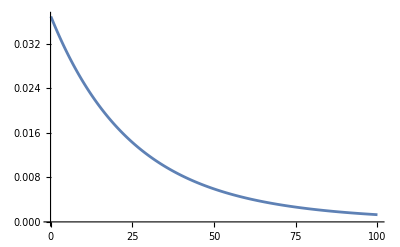

```mathematica
ListLinePlot[htab]
```

```mathematica
(*htab1= htable[100.1,1000,1000]*)
```

```mathematica
htab1 ={{100.1,0.0012896582112289},{100.33065405102548,0.0012816036636367528},{100.5618395834821,0.001273589734632992},{100.79355782202863,0.0012656163048390453},{101.02580999414575,0.0012576832545751347},{101.25859733014256,0.001249790463865405},{101.49192106316312,0.0012419378124426071},{101.72578242919289,0.0012341251797542804},{101.96018266706534,0.0012263524449664547},{102.19512301846852,0.0012186194869685369},{102.43060472795163,0.0012109261843791836},{102.66662904293158,0.001203272415550737},{102.90319721369966,0.0011956580585746805},{103.14031049342809,0.0011880829912855777},{103.3779701381767,0.001180547091266578},{103.61617740689961,0.0011730502358552294},{103.85493356145184,0.001165592302147232},{104.09423986659603,0.001158173167001802},{104.33409759000912,0.0011507927070464647},{104.5745080022891,0.0011434507986823994},{104.81547237696168,0.001136147318089655},{105.05699199048715,0.0011288821412308186},{105.29906812226695,0.001121655143856888},{105.54170205465068,0.001114466201512392},{105.7848950729427,0.0011073151895399042},{106.02864846540905,0.0011002019830851472},{106.27296352328422,0.0010931264571011979},{106.51784154077804,0.0010860884863545367},{106.76328381508246,0.001079087945429734},{107.0092916463785,0.0010721247087334227},{107.2558663378431,0.001065198650500009},{107.50300919565602,0.0010583096447962072},{107.75072152900675,0.0010514575655265327},{107.99900465010154,0.0010446422864375765},{108.24785987417013,0.0010378636811223536},{108.49728851947302,0.0010311216230264428},{108.74729190730815,0.0010244159854521334},{108.99787136201819,0.001017746641563283},{109.24902821099727,0.0010111134643899955},{109.50076378469822,0.0010045163268333933},{109.75307941663954,0.0009979551016713695},{110.0059764434125,0.0009914296615622842},{110.2594562046881,0.0009849398790498349},{110.51352004322436,0.0009784856265683771},{110.76816930487328,0.0009720667764474162},{111.02340533858805,0.0009656832009167106},{111.27922949643012,0.0009593347721101368},{111.53564313357644,0.0009530213620709051},{111.79264760832665,0.0009467428427569498},{112.05024428211011,0.0009404990860446525},{112.3084345194934,0.0009342899637339014},{112.56721968818724,0.0009281153475525538},{112.82660115905395,0.0009219751091615011},{113.08658030611461,0.0009158691201595524},{113.34715850655644,0.0009097972520869295},{113.60833714073992,0.0009037593764308091},{113.87011759220628,0.0008977553646298957},{114.13250124768473,0.0008917850880788613},{114.39548949709982,0.0008858484181329708},{114.65908373357885,0.0008799452261120145},{114.92328535345919,0.0008740753833059431},{115.18809575629571,0.000868238760979021},{115.45351634486816,0.0008624352303737881},{115.71954852518866,0.000856664662716065},{115.98619370650911,0.0008509269292192076},{116.25345330132863,0.0008452219010891413},{116.52132872540112,0.0008395494495282},{116.78982139774266,0.0008339094457392479},{117.05893274063911,0.0008283017609310542},{117.32866417965357,0.0008227262663221672},{117.59901714363407,0.0008171828331453188},{117.86999306472094,0.0008116713326516137},{118.14159337835457,0.0008061916361148453},{118.41381952328288,0.0008007436148366425},{118.68667294156907,0.0007953271401497897},{118.96015507859916,0.0007899420834226602},{119.23426738308967,0.0007845883160638535},{119.50901130709535,0.0007792657095262299},{119.78438830601677,0.0007739741353115062},{120.0603998386081,0.0007687134649735658},{120.33704736698489,0.0007634835701232202},{120.61433235663168,0.000758284322432774},{120.89225627640982,0.0007531155936394517},{121.17082059856533,0.0007479772555498266},{121.4500267987366,0.0007428691800436032},{121.72987635596222,0.0007377912390782345},{122.01037075268886,0.0007327433046929721},{122.29151147477907,0.0007277252490120877},{122.57330001151922,0.0007227369442495746},{122.85573785562731,0.000717778262713085},{123.13882650326096,0.00071284907680785},{123.42256745402521,0.0007079492590405724},{123.70696221098066,0.000703078682022864},{123.99201228065118,0.0006982372184760341},{124.27771917303218,0.0006934247412346346},{124.5640844015983,0.0006886411232498829},{124.85110948331169,0.000683886237593882},{125.13879593862991,0.0006791599574631922},{125.42714529151402,0.0006744621561831747},{125.71615906943661,0.0006697927072111347},{126.00583880338998,0.00066515148413985},{126.29618602789414,0.0006605383607020651},{126.58720228100506,0.0006559532107736687},{126.87888910432274,0.000651395908377518},{127.17124804299932,0.0006468663276867378},{127.46428064574744,0.0006423643430284523},{127.75798846484828,0.0006378898288879778},{128.0523730561598,0.0006334426599115465},{128.34743597912518,0.0006290227109100445},{128.64317879678075,0.0006246298568626701},{128.9396030757645,0.000620263972920383},{129.23671038632438,0.0006159249344095696},{129.53450230232656,0.0006116126168347447},{129.83298040126365,0.0006073268958824431},{130.1321462642633,0.0006030676474248831},{130.43200147609642,0.0005988347475227617},{130.7325476251856,0.0005946280724288047},{131.03378630361348,0.0005904474985907773},{131.33571910713135,0.0005862929026552086},{131.63834763516738,0.0005821641614706312},{131.94167349083526,0.0005780611520900719},{132.2456982809426,0.0005739837517748719},{132.5504236159995,0.000569931837997686},{132.85585111022704,0.0005659052884456934},{133.16198238156582,0.0005619039810235706},{133.46881905168468,0.0005579277938561563},{133.77636274598896,0.0005539766052923091},{134.0846150936295,0.0005500502939075245},{134.39357772751103,0.0005461487385067084},{134.70325228430085,0.0005422718181273301},{135.01364040443755,0.0005384194120422188},{135.3247437321397,0.0005345913997629532},{135.63656391541446,0.0005307876610421499},{135.9491026060665,0.0005270080758762358},{136.26236145970657,0.0005232525245088159},{136.57634213576034,0.0005195208874331173},{136.8910462974772,0.0005158130453948692},{137.20647561193906,0.0005121288793947305},{137.5226317500692,0.0005084682706911205},{137.83951638664104,0.0005048311008033878},{138.15713120028713,0.0005012172515137637},{138.47547787350797,0.0004976266048701571},{138.79455809268097,0.0004940590431888396},{139.1143735480693,0.0004905144490569951},{139.4349259338309,0.00048699270533545644},{139.7562169480275,0.0004834936951605208},{140.07824829263348,0.0004800173019469334},{140.4010216735451,0.0004765634093904537},{140.72453880058927,0.0004731319014699122},{141.04880138753285,0.0004697226624497465},{141.37381115209155,0.00046633557688205093},{141.69956981593913,0.00046297052960941475},{142.02607910471653,0.0004596274057670764},{142.35334074804092,0.0004563060907847012},{142.68135647951493,0.00045300647038907745},{143.01012803673584,0.00044972843060619414},{143.33965716130476,0.00044647185776354947},{143.66994559883582,0.00044323663849210647},{144.00099509896557,0.00044002265972814124},{144.33280741536194,0.0004368298087159614},{144.66538430573397,0.0004336579730096471},{144.99872753184061,0.000430507040474922},{145.33283885950058,0.0004273768992912792},{145.66772005860128,0.0004242674379538425},{146.00337290310844,0.0004211785452757485},{146.33979917107536,0.0004181101103895217},{146.67700064465242,0.0004150620227489375},{147.0149791100966,0.00041203417213131276},{147.35373635778063,0.0004090264486390221},{147.69327418220286,0.000406038742701475},{148.0335943819965,0.00040307094507650675},{148.3746987599393,0.0004001229468523311},{148.71658912296294,0.000397194639449595},{149.0592672821628,0.00039428591462248704},{149.4027350528074,0.00039139666446060006},{149.74699425434804,0.0003885267813905159},{150.09204671042855,0.00038567615817751617},{150.43789424889476,0.0003828446879272354},{150.7845387018044,0.0003800322640866625},{151.1319819054366,0.00037723878044607453},{151.48022570030173,0.00037446413114059103},{151.8292719311512,0.0003717082106513661},{152.1791224469871,0.00036897091380710576},{152.52977910107202,0.0003662521357852187},{152.88124375093903,0.0003635517721136054},{153.2335182584013,0.00036086971867187916},{153.58660448956203,0.00035820587169226595},{153.94050431482444,0.0003555601277612834},{154.2952196089016,0.0003529323838208365},{154.6507522508263,0.000350322537169621},{155.0071041239611,0.00034773048546410585},{155.36427711600828,0.0003451561267194826},{155.72227311901983,0.00034259935931136464},{156.08109402940744,0.000340060081976563},{156.44074174795267,0.00033753819381413663},{156.80121817981677,0.000335033594286455},{157.1625252345511,0.0003325461832201955},{157.52466482610706,0.00033007586080771324},{157.88763887284605,0.0003276225276075251},{158.25144929755007,0.0003251860845453144},{158.61609802743158,0.00032276643291512784},{158.9815869941437,0.0003203634743800861},{159.34791813379067,0.0003179771109733725},{159.7150933869379,0.00031560724509875247},{160.08311469862235,0.0003132537795315907},{160.45198401836277,0.00031091661741990264},{160.8217033001701,0.00030859566228466764},{161.19227450255778,0.00030629081802073353},{161.56369958855208,0.00030400198889748097},{161.9359805257026,0.00030172907955962813},{162.3091192860926,0.0002994719950279674},{162.68311784634952,0.000297230640699522},{163.0579781876554,0.0002950049223485616},{163.4337022957574,0.00029279474612718166},{163.81029216097832,0.0002906000185657105},{164.18774977822707,0.00028842064657329843},{164.56607714700937,0.00028625653743818833},{164.94527627143825,0.0002841075988286328},{165.32534916024474,0.00028197373879316573},{165.70629782678836,0.0002798548657607848},{166.08812428906793,0.0002777508885416294},{166.47083056973227,0.000275661716327252},{166.8544186960908,0.000273587258691168},{167.23889070012436,0.0002715274255889498},{167.62424861849593,0.0002694821273584222},{168.01049449256146,0.0002674512747203683},{168.39763036838073,0.00026543477877854127},{168.78565829672797,0.0002634325510198912},{169.17458033310308,0.00026144450331475874},{169.56439853774214,0.0002594705479170654},{169.95511497562856,0.0002575105974647984},{170.34673171650402,0.0002555645649797369},{170.7392508348793,0.0002536323638676479},{171.13267441004538,0.00025171390791860237},{171.52700452608437,0.0002498091113069077},{171.9222432718807,0.00024791788859130774},{172.31839274113193,0.0002460401547146893},{172.71545503236015,0.0002441758250043379},{173.11343224892286,0.00024232481517210585},{173.5123264990242,0.00024048704131403594},{173.91213989572609,0.00023866241991047895},{174.31287455695949,0.00023685086782592254},{174.71453260553554,0.0002350523023090916},{175.11711616915682,0.00023326664099283223},{175.52062738042875,0.0002314938018936317},{175.92506837687063,0.00022973370341179732},{176.33044130092722,0.00022798626433125974},{176.7367482999799,0.00022625140381931857},{177.14399152635815,0.00022452904142642455},{177.55217313735096,0.0002228190970857849},{177.9612952952182,0.00022112149111347645},{178.3713601672021,0.00021943614420801585},{178.78236992553872,0.00021776297744987764},{179.19432674746943,0.00021610191230140633},{179.60723281525256,0.00021445287060638626},{180.0210903161748,0.0002128157745898914},{180.43590144256294,0.00021119054685768795},{180.85166839179536,0.00020957711039577834},{181.26839336631375,0.0002079753885703556},{181.68607857363466,0.0002063853051271497},{182.10472622636138,0.00020480678419103918},{182.52433854219555,0.0002032397502655149},{182.94491774394885,0.00020168412823225686},{183.36646605955494,0.00020013984335089745},{183.78898572208107,0.0001986068212581459},{184.2124789697401,0.0001970849879673779},{184.6369480459021,0.00019557426986820613},{185.06239519910665,0.00019407459372587296},{185.48882268307423,0.00019258588668076223},{185.9162327567186,0.00019110807624754338},{186.34462768415852,0.00018964109031479072},{186.77400973472984,0.0001881848571444834},{187.2043811829975,0.00018673930537111745},{187.63574430876753,0.00018530436400117657},{188.0681013970992,0.00018387996241238489},{188.50145473831714,0.0001824660303532013},{188.93580662802336,0.00018106249794212157},{189.37115936710953,0.00017966929566667263},{189.80751526176905,0.00017828635438298996},{190.24487662350944,0.00017691360531503354},{190.68324576916436,0.00017555098005382101},{191.12262502090613,0.0001741984105566474},{191.56301670625774,0.0001728558291461597},{192.00442315810554,0.00017152316850990945},{192.44684671471123,0.00017020036169936706},{192.89028971972454,0.00016888734212900516},{193.33475452219542,0.00016758404357560455},{193.7802434765867,0.00016629040017734627},{194.22675894278632,0.0001650063464331438},{194.67430328612005,0.000163731817201541},{195.12287887736392,0.0001624667476998208},{195.57248809275674,0.00016121107350337016},{196.0231333140128,0.00015996473054461028},{196.47481692833435,0.0001587276551121254},{196.9275413284244,0.00015749978384964623},{197.38130891249924,0.00015628105375517848},{197.83612208430128,0.00015507140218025243},{198.29198325311165,0.00015387076682866265},{198.7488948337631,0.00015267908575559687},{199.20685924665273,0.00015149629736673544},{199.66587891775467,0.00015032234041723012},{200.12595627863325,0.00014915715401078608},{200.58709376645567,0.0001480006775983947},{201.04929382400474,0.0001468528509775434},{201.51255889969227,0.0001457136142912483},{201.9768914475717,0.00014458290802682697},{202.44229392735113,0.00014346067301495771},{202.9087688044064,0.0001423468504285146},{203.37631854979438,0.00014124138178170639},{203.84494564026554,0.00014014420892894446},{204.31465255827752,0.0001390552740635534},{204.78544179200816,0.00013797451971691346},{205.2573158353685,0.00013690188875731027},{205.73027718801634,0.00013583732438885435},{206.20432835536914,0.00013478077015030698},{206.67947184861745,0.00013373216991386882},{207.15571018473827,0.0001326914678843185},{207.63304588650826,0.0001316586085977286},{208.11148148251712,0.00013063353692024886},{208.59101950718107,0.00012961619804705249},{209.07166250075616,0.00012860653750113065},{209.55341300935194,0.00012760450113229353},{210.0362735849446,0.00012661003511578965},{210.52024678539087,0.0001256230859511276},{211.00533517444117,0.00012464360046110498},{211.49154132175366,0.000123671525790466},{211.9788678029074,0.00012270680940477531},{212.46731719941627,0.00012174939908909578},{212.95689209874263,0.0001207992429468719},{213.44759509431077,0.00011985628939886797},{213.93942878552113,0.00011892048718169137},{214.4323957777635,0.00011799178534668231},{214.92649868243123,0.00011707013325870412},{215.42174011693507,0.0001161554805949338},{215.91812270471664,0.0001152477773436621},{216.41564907526268,0.00011434697380284673},{216.91432186411907,0.00011345302057906375},{217.41414371290435,0.00011256586858628732},{217.91511726932416,0.00011168546904451013},{218.41724518718493,0.00011081177347854642},{218.92053012640827,0.00010994473371669099},{219.4249747530447,0.00010908430188962612},{219.93058173928804,0.0001082304304291007},{220.43735376348945,0.00010738307206648693},{220.9452935101716,0.00010654217983170213},{221.45440367004315,0.0001057077070518729},{221.96468694001248,0.00010487960735009934},{222.47614602320252,0.00010405783464410289},{222.98878362896468,0.00010324234314486167},{223.50260247289344,0.00010243308735556778},{224.01760527684064,0.00010163002207017762},{224.53379476892994,0.00010083310237209903},{225.05117368357108,0.00010004228363293832},{225.56974476147477,0.00009925752151118023},{226.0895107496668,0.00009847877195103536},{226.6104744015028,0.0000977059911809333},{227.13263847668279,0.00009693913571225684},{227.65600574126577,0.00009617816233817264},{228.18057896768445,0.00009542302813222814},{228.70636093475977,0.0000946736904470916},{229.23335442771582,0.00009393010691313049},{229.7615622381945,0.00009319223543719656},{230.29098716427032,0.00009246003420142067},{230.82163201046512,0.00009173346166170048},{231.3534995877631,0.00009101247654647389},{231.88659271362573,0.00009029703785541437},{232.42091421200632,0.00008958710485814697},{232.95646691336543,0.00008888263709296257},{233.4932536546857,0.00008818359436531897},{234.03127727948666,0.00008748993674671069},{234.57054063784014,0.00008680162457335758},{235.11104658638519,0.00008611861844480125},{235.65279798834317,0.00008544087922264109},{236.19579771353307,0.0000847683680291318},{236.74004863838644,0.00008410104624605028},{237.28555364596306,0.00008343887551329872},{237.83231562596575,0.00008278181772748156},{238.380337474756,0.00008212983504073763},{238.92962209536915,0.00008148288985937728},{239.4801723975299,0.00008084094484263461},{240.03199129766753,0.00008020396290126608},{240.58508171893152,0.0000795719071962066},{241.13944659120693,0.00007894474113744716},{241.69508885113012,0.0000783224283826053},{242.25201144210394,0.00007770493283561001},{242.81021731431372,0.00007709221864541776},{243.36970942474258,0.00007648425020470474},{243.93049073718728,0.00007588099214868498},{244.49256422227387,0.00007528240935363744},{245.0559328574735,0.00007468846693564288},{245.62059962711794,0.00007409913024939853},{246.18656752241571,0.00007351436488684042},{246.75383954146773,0.0000729341366759067},{247.32241868928327,0.00007235841167912898},{247.89230797779584,0.00007178715619244627},{248.46351042587915,0.0000712203367439958},{249.03602905936313,0.00007065792009266018},{249.6098669110499,0.00007009987322687555},{250.1850270207299,0.00006954616336332645},{250.76151243519797,0.00006899675794573069},{251.3393262082695,0.0000684516246435623},{251.91847140079656,0.00006791073135063742},{252.49895108068412,0.00006737404618400377},{253.0807683229064,0.0000668415374826583},{253.663926209523,0.00006631317380623966},{254.24842782969546,0.00006578892393378231},{254.8342762797033,0.00006526875686240047},{255.42147466296066,0.00006475264180618095},{256.01002609003274,0.00006424054819485974},{256.59993367865223,0.00006373244567248674},{257.1912005537357,0.00006322830409629549},{257.78382984740034,0.00006272809353541749},{258.3778246989805,0.00006223178426970556},{258.9731882550442,0.00006173934678841253},{259.56992366941,0.00006125075178893191},{260.1680341031635,0.00006076597017573147},{260.7675227246744,0.00006028497305900944},{261.3683927096127,0.000059807731753489534},{261.9706472409663,0.00005933421777719115},{262.5742895090572,0.00005886440285022878},{263.17932271155877,0.000058398258893701005},{263.7857500535125,0.00005793575802832065},{264.3935747473451,0.00005747687257327011},{265.0028000128855,0.00005702157504505946},{265.6134290773817,0.000056569838156290276},{266.2254651755183,0.00005612163481449811},{266.8389115494332,0.000055676938120860095},{267.453771448735,0.00005523572136911162},{268.0700481305202,0.000054797958044411026},{268.68774485939036,0.00005436362182204173},{269.30686490746956,0.000053932686566301795},{269.92741155442144,0.00005350512632931673},{270.549388087467,0.00005308091534993158},{271.1727978014015,0.00005266002805254694},{271.7976439986124,0.00005224243904584319},{272.42392998909656,0.00005182812312176577},{273.05165909047787,0.00005141705525435812},{273.68083462802485,0.00005100921059859179},{274.31145993466816,0.000050604564489237016},{274.9435383510183,0.000050203092439670475},{275.5770732253834,0.00004980477014088969},{276.2120679137869,0.000049409573460303624},{276.8485257799851,0.00004901747844056375},{277.48645019548553,0.00004862846129852772},{278.1258445395642,0.000048242498424114},{278.76671219928386,0.00004785956637926162},{279.40905656951185,0.0000474796418967329},{280.0528810529382,0.000047102701879017394},{280.6981890600932,0.00004672872339735416},{281.34498400936627,0.00004635768369055598},{281.99326932702326,0.00004598956016394056},{282.64304844722506,0.00004562433038823063},{283.2943248120458,0.00004526197209850333},{283.94710187149064,0.00004490246319319586},{284.6013830835147,0.00004454578173291037},{285.2571719140409,0.000044191905939400196},{285.91447183697846,0.00004384081419456132},{286.57328633424135,0.00004349248503934949},{287.23361889576665,0.00004314689717276783},{287.89547301953314,0.000042804029450726355},{288.5588522115797,0.00004246386088510244},{289.22375998602394,0.000042126370642737215},{289.8901998650809,0.00004179153804431013},{290.55817537908166,0.0000414593425633756},{291.22769006649185,0.00004112976382531028},{291.89874747393077,0.00004080278160637324},{292.5713511561898,0.00004047837583267326},{293.2455046762515,0.000040156526579077434},{293.92121160530843,0.00003983721406832692},{294.59847552278177,0.000039520418670015006},{295.2773000163409,0.00003920612089959796},{295.95768868192175,0.000038894301417396045},{296.63964512374616,0.00003858494102758215},{297.32317295434115,0.0000382780206773222},{298.0082757945577,0.00003797352145573518},{298.6949572735901,0.000037671424592897244},{299.3832210289951,0.00003737171145893904},{300.0730707067114,0.00003707436356306996},{300.7645099610786,0.00003677936255268692},{301.45754245485705,0.00003648669021234632},{302.1521718592467,0.000036196328462828914},{302.848401853907,0.00003590825936030344},{303.5462361269759,0.00003562246509531871},{304.2456783750901,0.00003533892799190488},{304.94673230340396,0.00003505763050662093},{305.6494016256094,0.000034778555227671976},{306.35369006395575,0.00003450168487406191},{307.05960134926903,0.000034227002294572114},{307.7671392209722,0.00003395449046691745},{308.4763074271045,0.00003368413249686842},{309.1871097243417,0.000033415911617356274},{309.89954987801593,0.00003314981118760437},{310.6136316621353,0.000032885814692164765},{311.3293588594041,0.000032623905740133816},{312.0467352612432,0.000032364068064290644},{312.7657646678095,0.00003210628552016691},{313.48645088801646,0.0000318505420852223},{314.20879773955426,0.00003159682185796333},{314.9328090489097,0.0000313451090571571},{315.6584886513869,0.00003109538802095899},{316.3858403911275,0.0000308476432060011},{317.11486812113066,0.00003060185918664916},{317.84557570327405,0.000030358020654144715},{318.5779670083339,0.000030116112415783196},{319.3120459160057,0.000029876119394075206},{320.04781631492443,0.000029638026625898545},{320.78528210268564,0.00002940181926179123},{321.52444718586594,0.000029167482565070857},{322.2653154800433,0.00002893500191101975},{323.00789090981834,0.000028704362786121353},{323.7521774088349,0.000028475550787251746},{324.49817891980064,0.00002824855162094791},{325.2458993945084,0.00002802335110253675},{325.9953427938568,0.000027799935155378044},{326.7465130878713,0.00002757828981015427},{327.4994142557252,0.00002735840120404684},{328.25405028576074,0.00002714025557999109},{329.0104251755104,0.00002692383928587957},{329.7685429317178,0.000026709138773845217},{330.52840757035887,0.000026496140599551023},{331.2900231166637,0.00002628483142135392},{332.0533936051371,0.000026075197999605376},{332.81852307958053,0.00002586722719592638},{333.5854155931133,0.000025660905972474275},{334.354075208194,0.000025456221391227252},{335.1245059966421,0.00002525316061318731},{335.8967120396595,0.000025051710897742547},{336.67069742785225,0.00002485185960195448},{337.446466261252,0.000024653594179797374},{338.2240226493379,0.00002445690218148441},{339.00337071105827,0.00002426177125273502},{339.7845145748525,0.000024068189134146872},{340.5674583786729,0.000023876143660467223},{341.3522062700066,0.000023685622759855695},{342.1387624058974,0.000023496614453275224},{342.927130952968,0.000023309106853785003},{343.7173160874421,0.00002312308816588436},{344.50932199516615,0.00002293854668481054},{345.30315287163205,0.00002275547079586069},{346.09881292199884,0.000022573848973810085},{346.8963063611155,0.00002239366978219522},{347.6956374135428,0.000022214921872654627},{348.496810313576,0.000022037593984299584},{349.2998293052673,0.000021861674943064488},{350.1046986424479,0.000021687153661110004},{350.91142258875095,0.00002151401913611412},{351.72000541763424,0.000021342260450659134},{352.5304514124024,0.000021171866771656346},{353.34276486622974,0.00002100282734967636},{354.15695008218324,0.00002083513151835137},{354.9730113732451,0.000020668768693720065},{355.79095306233563,0.000020503728373656053},{356.6107794823361,0.000020340000137291947},{357.4324949761119,0.000020177573644337696},{358.2561038965355,0.000020016438634525565},{359.08161060650895,0.000019856584927010596},{359.90901947898794,0.000019698002419794613},{360.73833489700445,0.000019540681089138866},{361.5695612536896,0.000019384610988921714},{362.4027029522978,0.000019229782250132066},{363.2377644062292,0.000019076185080284755},{364.0747500390538,0.000018923809762820567},{364.9136642845344,0.00001877264665655247},{365.75451158665004,0.000018622686195081244},{366.5972963996202,0.000018473918886293092},{367.4420231879276,0.00001832633531176936},{368.28869642634214,0.000018179926126197778},{369.1373205999449,0.000018034682056881152},{369.98790020415146,0.000017890593903171267},{370.840439744736,0.000017747652535945215},{371.6949437378549,0.000017605848897038586},{372.55141671007095,0.000017465173998701477},{373.4098631983773,0.000017325618923139022},{374.27028775022126,0.000017187174821928496},{375.1326949235287,0.0000170498329155008},{375.9970892867277,0.00001691358449262838},{376.8634754187735,0.000016778420909909826},{377.731857909172,0.000016644333591298264},{378.6022413580045,0.000016511314027522547},{379.47463037595213,0.00001637935377561106},{380.34902958431996,0.000016248444458421294},{381.22544361506164,0.00001611857776411397},{382.103877110804,0.000015989745445674012},{382.9843347248715,0.000015861939320381506},{383.866821121311,0.000015735151269367056},{384.7513409749165,0.000015609373237144105},{385.6378989712537,0.000015484597231071468},{386.52649980668514,0.000015360815320908544},{387.4171481883946,0.000015238019638337487},{388.3098488344126,0.000015116202376509458},{389.2046064736409,0.000014995355789574709},{390.101425845878,0.000014875472192169934},{391.00031170184377,0.000014756543959019777},{391.9012688032051,0.000014638563524469566},{392.8043019226006,0.000014521523382010725},{393.7094158436664,0.00001440541608384103},{394.6166153610613,0.000014290234240395044},{395.5259052804919,0.000014175970519957433},{396.43729041873837,0.000014062617648183585},{397.35077560367995,0.000013950168407639134},{398.2663656743204,0.000013838615637409157},{399.1840654808138,0.000013727952232646445},{400.1038798844899,0.000013618171144166648},{401.02581375788026,0.000013509265377985628},{401.9498719847439,0.000013401227994899535},{402.8760594600932,0.000013294052110116708},{403.8043810902197,0.000013187730892796985},{404.73484179272026,0.000013082257565644773},{405.66744649652304,0.00001297762540449698},{406.60220014191356,0.000012873827737924073},{407.53910768056096,0.00001277085794685364},{408.4781740755444,0.000012668709464112822},{409.41940430137885,0.000012567375774053113},{410.36280334404177,0.00001246685041217884},{411.30837620099965,0.00001236712696473243},{412.25612788123425,0.000012268199068318108},{413.2060634052691,0.000012170060409478938},{414.1581878051964,0.00001207270472435228},{415.1125061247034,0.000011976125798299918},{416.0690234190991,0.00001188031746548117},{417.02774475534125,0.000011785273608508363},{417.988675212063,0.00001169098815806169},{418.95181987959984,0.000011597455092543115},{419.91718386001685,0.000011504668437698274},{420.884772267135,0.000011412622266213604},{421.8545902265592,0.00001132131069740761},{422.82664287570464,0.000011230727896856089},{423.8009353638245,0.00001114086807602807},{424.77747285203685,0.000011051725491930466},{425.7562605133525,0.00001096329444674411},{426.7373035327019,0.000010875569287521378},{427.7206071069628,0.000010788544405805515},{428.7061764449879,0.000010702214237272435},{429.6940167676321,0.00001061657326142008},{430.6841333077807,0.000010531616001216857},{431.67653131037656,0.000010447337022784212},{432.6712160324482,0.000010363730935030329},{433.66819274313764,0.000010280792389321436},{434.6674667237282,0.00001019851607919626},{435.66904326767246,0.000010116896740000531},{436.67292768062043,0.00001003592914857215},{437.6791252804476,9.955608122913046*^-6},{438.6876413972831,9.875928521879834*^-6},{439.69848137353785,9.796885244891858*^-6},{440.7116505639331,9.71847323156408*^-6},{441.72715433552855,9.64068746142232*^-6},{442.7449980677509,9.563522953604254*^-6},{443.7651871524223,9.486974766541422*^-6},{444.7877269937889,9.411037997662154*^-6},{445.81262300854956,9.335707783055988*^-6},{446.83988062588446,9.260979297212647*^-6},{447.86950528748395,9.186847752725314*^-6},{448.90150244757734,9.11330839996208*^-6},{449.9358775729616,9.04035652679239*^-6},{450.97263614303074,8.967987458286499*^-6},{452.0117836498043,8.89619655644854*^-6},{453.0533255979571,8.824979219916908*^-6},{454.0972675048476,8.75433088364987*^-6},{455.1436149005479,8.684247018685687*^-6},{456.19237332787264,8.614723131849027*^-6},{457.24354834240825,8.545754765467765*^-6},{458.29714551254256,8.477337497094218*^-6},{459.3531704194945,8.409466939218862*^-6},{460.41162865734333,8.342138739040703*^-6},{461.47252583305817,8.275348578163344*^-6},{462.53586756652845,8.209092172319235*^-6},{463.6016594905925,8.143365271125585*^-6},{464.66990725106854,8.078163657808869*^-6},{465.74061650678374,8.013483148963492*^-6},{466.813792929605,7.949319594256072*^-6},{467.8894422044681,7.885668876177427*^-6},{468.96757002940836,7.822526909816018*^-6},{470.04818211559086,7.759889642574035*^-6},{471.13128418734044,7.697753053923904*^-6},{472.21688198217214,7.636113155146422*^-6},{473.30498125082164,7.574965989097205*^-6},{474.39558775727573,7.514307629974842*^-6},{475.48870727880256,7.4541341830354716*^-6},{476.5843456059828,7.394441784371128*^-6},{477.6825085427396,7.33522660067623*^-6},{478.78320190637,7.276484829001999*^-6},{479.88643152757544,7.2182126965241254*^-6},{480.9922032504926,7.1604064602790645*^-6},{482.1005229327244,7.1030624069645935*^-6},{483.21139644537124,7.04617685270772*^-6},{484.32482967306163,6.989746142807566*^-6},{485.44082851398406,6.933766651524947*^-6},{486.5593988799173,6.878234781843604*^-6},{487.6805466962627,6.823146965270052*^-6},{488.8042779020751,6.768499661594596*^-6},{489.9305984500942,6.714289358647631*^-6},{491.05951430677607,6.660512572116194*^-6},{492.1910314523253,6.607165845310806*^-6},{493.32515588072584,6.554245748952639*^-6},{494.46189359977353,6.501748880948357*^-6},{495.60125063110746,6.4496718661725614*^-6},{496.743233010242,6.3980113562898594*^-6},{497.88784678659886,6.346764029515359*^-6},{499.03509802353886,6.295926590403912*^-6},{500.1849927983944,6.2454957696562066*^-6},{501.3375372025014,6.1954683239088915*^-6},{502.49273734123165,6.14584103554624*^-6},{503.65059933402534,6.096610712468412*^-6},{504.81112931442306,6.0477741879003134*^-6},{505.97433343009874,5.999328320216481*^-6},{507.1402178428917,5.951269992719203*^-6},{508.30878872883994,5.903596113451398*^-6},{509.48005227821227,5.856303614989732*^-6},{510.65401469554143,5.809389454266429*^-6},{511.83068219965696,5.7628506123903385*^-6},{513.0100610237179,5.716684094420613*^-6},{514.1921574152459,5.67088692920039*^-6},{515.3769776361587,5.625456169170102*^-6},{516.5645279628026,5.58038889018264*^-6},{517.7548146859864,5.535682191320248*^-6},{518.9478441110142,5.491333194687322*^-6},{520.143622557719,5.447339045261987*^-6},{521.3421563604963,5.403696910710035*^-6},{522.5434518683378,5.360403981190451*^-6},{523.7475154448641,5.317457469188279*^-6},{524.9543534683595,5.2748546093305445*^-6},{526.1639723318056,5.232592658234103*^-6},{527.3763784429144,5.1906688943165076*^-6},{528.5915782241634,5.1490806176091055*^-6},{529.8095781128283,5.107825149614195*^-6},{531.0303845610184,5.066899833124996*^-6},{532.2540040357101,5.026302032061268*^-6},{533.4804430187809,4.986029131293192*^-6},{534.7097080070441,4.946078536472483*^-6},{535.9418055122837,4.906447673897973*^-6},{537.1767420612881,4.867133990326228*^-6},{538.4145241958846,4.828134952810782*^-6},{539.655158472975,4.789448048550323*^-6},{540.8986514645694,4.751070784726429*^-6},{542.1450097578215,4.7130006883614344*^-6},{543.3942399550632,4.675235306132177*^-6},{544.6463486738401,4.6377722042280385*^-6},{545.9013425469457,4.600608968211978*^-6},{547.1592282224572,4.563743202850402*^-6},{548.4200123637709,4.527172531968854*^-6},{549.6837016496366,4.490894598287676*^-6},{550.9503027741939,4.454907063290228*^-6},{552.2198224470069,4.419207607080305*^-6},{553.4922673931007,4.3837939282085135*^-6},{554.767644352996,4.348663743543162*^-6},{556.0459600827451,4.3138147881252575*^-6},{557.3272213539683,4.2792448150278565*^-6},{558.6114349538892,4.244951595212249*^-6},{559.8986076853705,4.210932917367288*^-6},{561.1887463669506,4.17718658779622*^-6},{562.4818578328793,4.143710430272263*^-6},{563.777948933154,4.1105022858878316*^-6},{565.0770265335565,4.077560012925934*^-6},{566.3790975156884,4.044881486715532*^-6},{567.6841687770087,4.012464599518666*^-6},{568.9922472308695,3.980307260380038*^-6},{570.3033398065527,3.948407394983542*^-6},{571.6174534493075,3.916762945543241*^-6},{572.934595120386,3.885371870661476*^-6},{574.2547717970812,3.8542321452065205*^-6},{575.5779904727626,3.823341760170294*^-6},{576.904258156915,3.7926987225420523*^-6},{578.2335818751743,3.7623010552041736*^-6},{579.5659686693651,3.7321467967840338*^-6},{580.901425597538,3.7022340015324562*^-6},{582.2399597340071,3.672560739202519*^-6},{583.5815781693874,3.6431250949283956*^-6},{584.9262880106324,3.6139251691138073*^-6},{586.2740963810716,3.5849590772871387*^-6},{587.6250104204483,3.556224949992879*^-6},{588.9790372849576,3.5277209326840594*^-6},{590.3361841472839,3.499445185591136*^-6},{591.6964581966397,3.4713958836106768*^-6},{593.0598666388025,3.443571216176567*^-6},{594.426416696154,3.4159693871606898*^-6},{595.7961156077178,3.388588614762772*^-6},{597.168970629198,3.361427131373953*^-6},{598.5449890330178,3.3344831834801306*^-6},{599.9241781083572,3.3077550315465403*^-6},{601.3065451611927,3.281240949913228*^-6},{602.6920975143354,3.2549392266814763*^-6},{604.0808425074696,3.228848163588483*^-6},{605.4727874971924,3.2029660759239918*^-6},{606.8679398570517,3.177291292414671*^-6},{608.2663069775865,3.151822155111819*^-6},{609.6678962663647,3.1265570192882884*^-6},{611.0727151480233,3.101494253328515*^-6},{612.4807710643075,3.0766322386431997*^-6},{613.8920714741098,3.0519693695500805*^-6},{615.3066238535098,3.0275040531654687*^-6},{616.7244356958139,3.003234709318415*^-6},{618.1455145115946,2.9791597704427384*^-6},{619.5698678287308,2.955277681482623*^-6},{620.9975031924474,2.9315868997813583*^-6},{622.4284281653552,2.908085894984593*^-6},{623.8626503274907,2.8847731489613814*^-6},{625.3001772763573,2.8616471556880494*^-6},{626.7410166269642,2.83870642115578*^-6},{628.1851760118678,2.8159494632757325*^-6},{629.6326630812115,2.7933748117863854*^-6},{631.0834855027665,2.7709810081693375*^-6},{632.5376509619723,2.748766605533243*^-6},{633.9951671619776,2.726730168534294*^-6},{635.456041823681,2.704870273290528*^-6},{636.9202826857714,2.6831855072825567*^-6},{638.3878975047703,2.6616744692676894*^-6},{639.8588940550712,2.6403357691776995*^-6},{641.3332801289823,2.619168028046958*^-6},{642.8110635367667,2.598169877923892*^-6},{644.2922521066845,2.577339961767661*^-6},{645.7768536850336,2.5566769333725968*^-6},{647.264876136192,2.5361794572789575*^-6},{648.7563273426589,2.5158462086945797*^-6},{650.2512152050963,2.495675873404872*^-6},{651.7495476423721,2.4756671476768964*^-6},{653.2513325916004,2.455818738195748*^-6},{654.7565780081844,2.4361293619752114*^-6},{656.2652918658586,2.4165977462713486*^-6},{657.7774821567306,2.3972226285027077*^-6},{659.293156891324,2.3780027561647612*^-6},{660.8123240986205,2.358936886766902*^-6},{662.3349918261022,2.340023787737714*^-6},{663.8611681397948,2.321262236342472*^-6},{665.39086112431,2.3026510196173374*^-6},{666.9240788828881,2.284188934284919*^-6},{668.4608295374414,2.2658747866846796*^-6},{670.0011212285971,2.2477073926826952*^-6},{671.5449621157398,2.2296855776005964*^-6},{673.0923603770561,2.2118081761538743*^-6},{674.6433242095765,2.194074032361668*^-6},{676.1978618292193,2.176481999477237*^-6},{677.7559814708346,2.15903093991175*^-6},{679.3176913882473,2.1417197251666318*^-6},{680.8829998543013,2.1245472357666695*^-6},{682.4519151609024,2.1075123611705153*^-6},{684.0244456190641,2.090613999710171*^-6},{685.6005995589493,2.073851058524413*^-6},{687.180385329916,2.057222453483445*^-6},{688.7638113005615,2.040727109121917*^-6},{690.3508858587658,2.0243639585594847*^-6},{691.9416174117364,2.0081319434469334*^-6},{693.5360143860536,1.992030013897748*^-6},{695.1340852277142,1.976057128407404*^-6},{696.7358384021766,1.9602122537966376*^-6},{698.3412823944054,1.9444943651407984*^-6},{699.950425708917,1.928902445712406*^-6},{701.5632768698239,1.9134354869097434*^-6},{703.1798444208804,1.8980924881826332*^-6},{704.8001369255273,1.882872456985814*^-6},{706.4241629669378,1.8677744087073924*^-6},{708.051931148063,1.8527973666054029*^-6},{709.6834500916766,1.8379403617431028*^-6},{711.3187284404219,1.8232024329247983*^-6},{712.9577748568564,1.8085826266483197*^-6},{714.6005980234983,1.7940799970298635*^-6},{716.2472066428726,1.7796936057425068*^-6},{717.8976094375566,1.7654225219637006*^-6},{719.551815150227,1.7512658223120643*^-6},{721.209832543705,1.7372225907934954*^-6},{722.8716704010039,1.7232919187304907*^-6},{724.5373375253752,1.7094729047084622*^-6},{726.2068427403548,1.6957646545284535*^-6},{727.8801948898102,1.682166281137187*^-6},{729.5574028379879,1.668676904573952*^-6},{731.2384754695585,1.6552956519110583*^-6},{732.923421689666,1.6420216572027022*^-6},{734.6122504239736,1.6288540614342987*^-6},{736.3049706187113,1.615792012451103*^-6},{738.0015912407235,1.6028346649143254*^-6},{739.7021212775161,1.5899811802478996*^-6},{741.4065697373045,1.5772307265821551*^-6},{743.114945649061,1.5645824787017606*^-6},{744.827258062563,1.5520356179827885*^-6},{746.5435160484407,1.5395893323545844*^-6},{748.2637286982248,1.5272428162442746*^-6},{749.9879051243954,1.5149952705165591*^-6},{751.7160544604302,1.5028459024287955*^-6},{753.4481858608517,1.4907939255767874*^-6},{755.1843085012775,1.4788385598523262*^-6},{756.9244315784674,1.4669790313860054*^-6},{758.668564310373,1.4552145724913344*^-6},{760.416715936186,1.443544421628503*^-6},{762.1688957163877,1.4319678233496635*^-6},{763.9251129327974,1.4204840282502392*^-6},{765.6853768886223,1.409092292918403*^-6},{767.4496969085059,1.397791879885869*^-6},{769.2180823385781,1.386582057592657*^-6},{770.9905425465049,1.3754621003277469*^-6},{772.7670869215368,1.3644312881824842*^-6},{774.54772487456,1.3534889070101324*^-6},{776.3324658381455,1.3426342483768848*^-6},{778.1213192665988,1.3318666095221818*^-6},{779.9142946360109,1.3211852933012958*^-6},{781.7114014443075,1.3105896081465939*^-6},{783.5126492113001,1.3000788680302275*^-6},{785.3180474787357,1.289652392410232*^-6},{787.1276058103481,1.2793095061906717*^-6},{788.9413337919082,1.2690495396735486*^-6},{790.7592410312744,1.2588718285225253*^-6},{792.5813371584444,1.248775713722063*^-6},{794.4076318256053,1.238760541522885*^-6},{796.2381347071852,1.228825663408495*^-6},{798.0728554999044,1.2189704360536487*^-6},{799.911803922827,1.209194221282372*^-6},{801.7549897174116,1.1994963860266031*^-6},{803.6024226475636,1.1898763022779105*^-6},{805.4541124996873,1.1803333470589553*^-6},{807.3100690827362,1.1708669023805678*^-6},{809.1703022282667,1.1614763551951629*^-6},{811.0348217904893,1.152161097362604*^-6},{812.9036376463207,1.1429205256076806*^-6},{814.7767596954365,1.1337540414892525*^-6},{816.6541978603234,1.1246610513547036*^-6},{818.5359620863319,1.1156409662969966*^-6},{820.4220623417293,1.106693202128058*^-6},{822.3125086177514,1.0978171793350732*^-6},{824.2073109286567,1.0890123230452396*^-6},{826.1064793117788,1.0802780629843735*^-6},{828.0100238275797,1.071613833440697*^-6},{829.9179545597032,1.063019073238142*^-6},{831.8302816150277,1.0544932256892552*^-6},{833.747015123721,1.0460357385610146*^-6},{835.6681652392925,1.0376460640418852*^-6},{837.5937421386479,1.0293236587060328*^-6},{839.5237560221434,1.0210679834820785*^-6},{841.4582171136384,1.012878503608298*^-6},{843.397135660551,1.0047546886037618*^-6},{845.3405219339116,9.966960122393006*^-7},{847.288386228418,9.887019524964014*^-7},{849.2407388624882,9.807719915363622*^-7},{851.1975901783177,9.729056156628661*^-7},{853.1589505419319,9.65102315294945*^-7},{855.1248303432421,9.573615849356776*^-7},{857.0952399961008,9.496829231290418*^-7},{859.0701899383564,9.42065832435567*^-7},{861.0496906319081,9.345098193992081*^-7},{863.0337525627623,9.270143945164015*^-7},{865.0223862410874,9.195790722035901*^-7},{867.0156022012693,9.122033707592067*^-7},{869.013411001969,9.048868123439302*^-7},{871.0158232261758,8.9762892294564*^-7},{873.0228494812651,8.904292323452607*^-7},{875.034500399054,8.832872740892069*^-7},{877.0507866358583,8.762025854570328*^-7},{879.0717188725482,8.691747074389779*^-7},{881.0973078146052,8.622031846990574*^-7},{883.1275641921786,8.552875655433834*^-7},{885.1624987601427,8.484274018989902*^-7},{887.2021222981537,8.416222492808485*^-7},{889.2464456107058,8.348716667648323*^-7},{891.2954795271909,8.281752169551195*^-7},{893.3492349019526,8.215324659569782*^-7},{895.4077226143469,8.149429833566162*^-7},{897.4709535687977,8.084063421843187*^-7},{899.5389386948552,8.019221188885145*^-7},{901.6116889472543,7.954898933102303*^-7},{903.6892153059719,7.891092486556868*^-7},{905.7715287762852,7.827797714732047*^-7},{907.8586403888308,7.765010516168814*^-7},{909.9505611996618,7.70272682226181*^-7},{912.0473022903075,7.640942597028395*^-7},{914.1488747678314,7.579653836794919*^-7},{916.2552897648903,7.518856569964195*^-7},{918.3665584397935,7.458546856712131*^-7},{920.4826919765616,7.398720788802817*^-7},{922.6037015849857,7.339374489331656*^-7},{924.729598500687,7.280504112399389*^-7},{926.8603939851762,7.222105842925201*^-7},{928.9960993259132,7.164175896387636*^-7},{931.1367258363667,7.106710518599586*^-7},{933.2822848560749,7.049705985445178*^-7},{935.432787750704,6.993158602592889*^-7},{937.5882459121104,6.937064705346283*^-7},{939.7486707583994,6.881420658373655*^-7},{941.9140737339862,6.82622285544533*^-7},{944.0844663096574,6.771467719220574*^-7},{946.2598599826301,6.71715170099744*^-7},{948.4402662766144,6.663271280549981*^-7},{950.625696741873,6.609822965834596*^-7},{952.8161629552841,6.556803292748434*^-7},{955.0116765204011,6.504208824972647*^-7},{957.2122490675148,6.452036153710724*^-7},{959.4178922537152,6.400281897494595*^-7},{961.6286177629527,6.348942701915851*^-7},{963.8444373061002,6.298015239429403*^-7},{966.0653626210159,6.247496209199237*^-7},{968.2914054726039,6.19738233680654*^-7},{970.5225776528779,6.147670374061803*^-7},{972.758890981023,6.098357098793706*^-7},{975.000357303459,6.049439314655372*^-7},{977.2469884939021,6.000913850938965*^-7},{979.4987964534286,5.952777562293575*^-7},{981.7557931105373,5.905027328575441*^-7},{984.0179904212137,5.857660054665346*^-7},{986.2854003689921,5.810672670233925*^-7},{988.5580349650202,5.764062129557332*^-7},{990.835906248122,5.717825411283191*^-7},{993.1190262848618,5.671959518294582*^-7},{995.407407169608,5.626461477511428*^-7},{997.7010610245976,5.58132833963512*^-7},{999.9999999999999,5.536557179011461*^-7}}
```

```mathematica
htab01 = Join[htab, htab1];
```

```mathematica
htab1
```

htab1

```mathematica
Dimensions[htab01]
```

{2002,2}

```mathematica
lhinterp=Interpolation@Log[htab01];
```

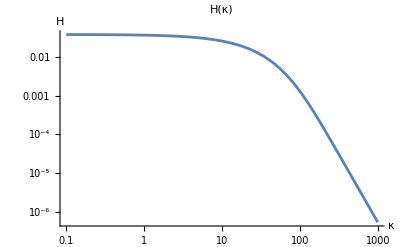

```mathematica
LogLogPlot[Exp[lhinterp[Log[k]]],{k,0.1,1000}, PlotLabel->"H(κ)", AxesLabel->{κ, H}]
```

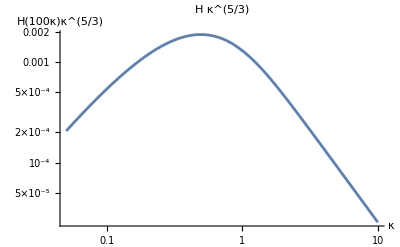

```mathematica
LogLogPlot[Exp[lhinterp[Log[100k]]+ 5/3 Log[k]],{k,0.05,10}, PlotLabel->"H κ^(5/3)", AxesLabel->{κ, "H(100κ)κ^(5/3)"}]
```

```mathematica
SPIndex[κ_]:= Evaluate[-D[lhinterp[t],t]/.t->Log[κ]];
```

```mathematica
SPIndex[1000.]
```

3.4993

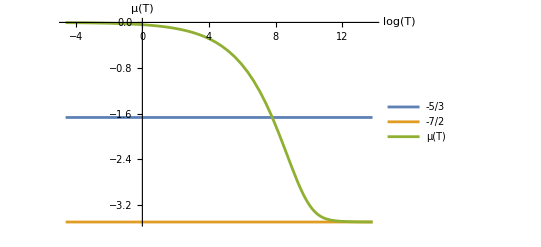

```mathematica
Plot[{-5/3,-7/2,-SPIndex[Exp[x/2]]},{x,Log[0.01],Log[10^6]}, 
PlotLegends->{-5/3,-7/2,μ[T]},
AxesLabel->{Log[T], μ[T]}]
```

```mathematica
EDis[t_] := With[{x0=1000},(NIntegrate[Exp[lhinterp[Log[x]]] x^2 ,{x, Sqrt[t],x0}] + 
Exp[lhinterp[Log[x0]]]2 x0^3)]
```

```mathematica
EDis[0]
```

4499.66

```mathematica
etable[k0_, k1_, M_] := 
ParallelTable[
Block[{k},
k = N[k0 (k1/k0)^(n/M )];
{k,EDis[k^2]}]
,{n,0,M}];
```

```mathematica
etab = etable[0.1, 1000, 1000];
```

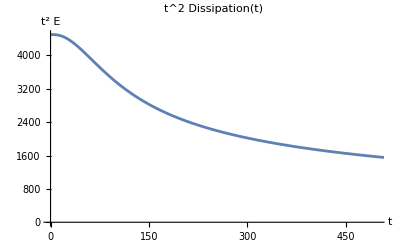

```mathematica
ListLinePlot[etab, PlotLabel->"t^2 Dissipation(t) ", AxesLabel->{t,t^2 Ε}]
```

```mathematica
einterp = Interpolation[{#[[1]],Log[#[[2]]]} &/@etab];
```

```mathematica
EEAll[t_] :=Exp[einterp[Sqrt[t]]]/t^2;
```

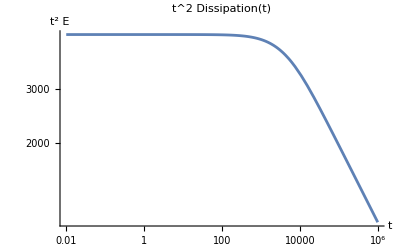

```mathematica
LogLogPlot[Exp[einterp[Sqrt[t]]],{t,0.1^2,1000^2}, PlotLabel->"t^2 Dissipation(t)", AxesLabel->{t,t^2 Ε}, PlotRange->All]
```

```mathematica
einterp[0]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

8.41176

```mathematica
x = .;
```

```mathematica
n[t_] :=Evaluate[1 - 1/2x D[einterp[x],x]/.x->Sqrt[t]];
```

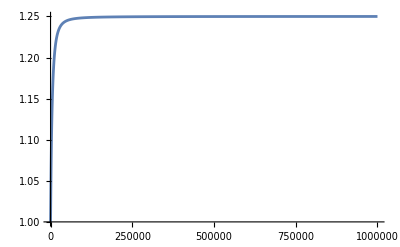

```mathematica
Plot[n[t],{t,0.1^2,1000^2}, PlotRange->All]
```

```mathematica
FindMinimum[{n[z], 0.1^2 < z < 1000^2},z]
```

{1.,{z→0.0801557}}

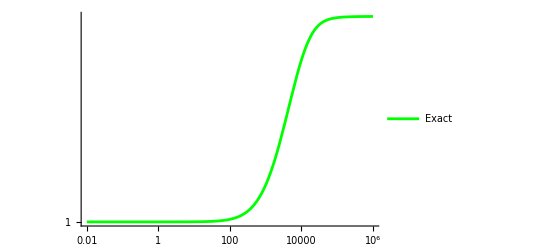

```mathematica
P1 =LogLogPlot[n[t],{t,0.1^2,1000^2}, PlotStyle->Green,PlotLegends->{"Exact"}, PlotRange->All]
```

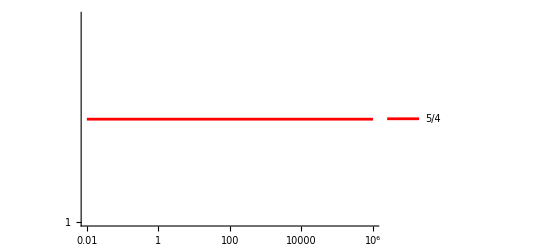

```mathematica
P2 = LogLogPlot[5/4,{t,0.1^2,1000^2}, PlotStyle->Red, PlotLegends->{5/4}]
```

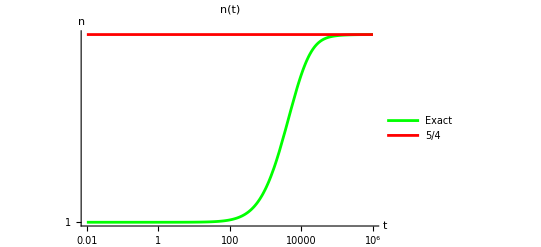

```mathematica
Show[{P1,P2}, PlotLabel->"n(t)", AxesLabel->{t, n}]
```

```mathematica
TailE = Integrate[(1/x)^(9/4),{x,t0, Infinity}, GenerateConditions->False]
```

4/5 (1/t0)^(5/4)

```mathematica
EDec[t_] :=With[{t0 = 1000^2},NIntegrate[EEAll[x],{x,t,t0}] + EEAll[t0]4/5 t0];
```

```mathematica
EDec[1000]
```

3.97548

```mathematica
edectable[k0_, k1_, M_] :=  
ParallelTable[Block[{k},
k = N[k0 (k1/k0)^(n/M )];
{Log[k^2], Log[k^2 EDec[k^2]]}]
,{n,0,M}];
```

```mathematica
edectab =edectable[0.1, 1000,1000]
```

{{-4.60517,8.41175},{-4.58675,8.41175},{-4.56833,8.41175},{-4.54991,8.41175},{-4.53149,8.41175},{-4.51307,8.41175},{-4.49465,8.41175},{-4.47623,8.41175},{-4.4578,8.41175},{-4.43938,8.41175},{-4.42096,8.41175},{-4.40254,8.41175},{-4.38412,8.41175},{-4.3657,8.41175},{-4.34728,8.41175},{-4.32886,8.41175},{-4.31044,8.41175},{-4.29202,8.41175},{-4.2736,8.41175},{-4.25518,8.41175},{-4.23676,8.41175},{-4.21834,8.41175},{-4.19992,8.41175},{-4.18149,8.41175},{-4.16307,8.41175},{-4.14465,8.41175},{-4.12623,8.41175},{-4.10781,8.41175},{-4.08939,8.41175},{-4.07097,8.41175},{-4.05255,8.41175},{-4.03413,8.41175},{-4.01571,8.41175},{-3.99729,8.41175},{-3.97887,8.41175},{-3.96045,8.41175},{-3.94203,8.41175},{-3.9236,8.41175},{-3.90518,8.41175},{-3.88676,8.41175},{-3.86834,8.41175},{-3.84992,8.41175},{-3.8315,8.41175},{-3.81308,8.41175},{-3.79466,8.41175},{-3.77624,8.41175},{-3.75782,8.41175},{-3.7394,8.41175},{-3.72098,8.41175},{-3.70256,8.41175},{-3.68414,8.41175},{-3.66572,8.41175},{-3.64729,8.41175},{-3.62887,8.41175},{-3.61045,8.41175},{-3.59203,8.41175},{-3.57361,8.41175},{-3.55519,8.41175},{-3.53677,8.41175},{-3.51835,8.41175},{-3.49993,8.41175},{-3.48151,8.41175},{-3.46309,8.41175},{-3.44467,8.41175},{-3.42625,8.41175},{-3.40783,8.41175},{-3.38941,8.41175},{-3.37098,8.41175},{-3.35256,8.41175},{-3.33414,8.41175},{-3.31572,8.41175},{-3.2973,8.41175},{-3.27888,8.41175},{-3.26046,8.41175},{-3.24204,8.41175},{-3.22362,8.41175},{-3.2052,8.41175},{-3.18678,8.41175},{-3.16836,8.41175},{-3.14994,8.41175},{-3.13152,8.41175},{-3.1131,8.41175},{-3.09467,8.41175},{-3.07625,8.41175},{-3.05783,8.41175},{-3.03941,8.41175},{-3.02099,8.41175},{-3.00257,8.41175},{-2.98415,8.41175},{-2.96573,8.41175},{-2.94731,8.41175},{-2.92889,8.41174},{-2.91047,8.41174},{-2.89205,8.41174},{-2.87363,8.41174},{-2.85521,8.41174},{-2.83678,8.41174},{-2.81836,8.41174},{-2.79994,8.41174},{-2.78152,8.41174},{-2.7631,8.41174},{-2.74468,8.41174},{-2.72626,8.41174},{-2.70784,8.41174},{-2.68942,8.41174},{-2.671,8.41174},{-2.65258,8.41174},{-2.63416,8.41174},{-2.61574,8.41174},{-2.59732,8.41174},{-2.5789,8.41174},{-2.56047,8.41174},{-2.54205,8.41174},{-2.52363,8.41174},{-2.50521,8.41174},{-2.48679,8.41174},{-2.46837,8.41174},{-2.44995,8.41174},{-2.43153,8.41174},{-2.41311,8.41174},{-2.39469,8.41174},{-2.37627,8.41174},{-2.35785,8.41174},{-2.33943,8.41174},{-2.32101,8.41173},{-2.30259,8.41173},{-2.28416,8.41173},{-2.26574,8.41173},{-2.24732,8.41173},{-2.2289,8.41173},{-2.21048,8.41173},{-2.19206,8.41173},{-2.17364,8.41173},{-2.15522,8.41173},{-2.1368,8.41173},{-2.11838,8.41173},{-2.09996,8.41173},{-2.08154,8.41173},{-2.06312,8.41173},{-2.0447,8.41173},{-2.02627,8.41173},{-2.00785,8.41173},{-1.98943,8.41173},{-1.97101,8.41173},{-1.95259,8.41172},{-1.93417,8.41172},{-1.91575,8.41172},{-1.89733,8.41172},{-1.87891,8.41172},{-1.86049,8.41172},{-1.84207,8.41172},{-1.82365,8.41172},{-1.80523,8.41172},{-1.78681,8.41172},{-1.76839,8.41172},{-1.74996,8.41172},{-1.73154,8.41172},{-1.71312,8.41172},{-1.6947,8.41172},{-1.67628,8.41171},{-1.65786,8.41171},{-1.63944,8.41171},{-1.62102,8.41171},{-1.6026,8.41171},{-1.58418,8.41171},{-1.56576,8.41171},{-1.54734,8.41171},{-1.52892,8.41171},{-1.5105,8.41171},{-1.49208,8.41171},{-1.47365,8.4117},{-1.45523,8.4117},{-1.43681,8.4117},{-1.41839,8.4117},{-1.39997,8.4117},{-1.38155,8.4117},{-1.36313,8.4117},{-1.34471,8.4117},{-1.32629,8.4117},{-1.30787,8.4117},{-1.28945,8.41169},{-1.27103,8.41169},{-1.25261,8.41169},{-1.23419,8.41169},{-1.21576,8.41169},{-1.19734,8.41169},{-1.17892,8.41169},{-1.1605,8.41169},{-1.14208,8.41168},{-1.12366,8.41168},{-1.10524,8.41168},{-1.08682,8.41168},{-1.0684,8.41168},{-1.04998,8.41168},{-1.03156,8.41168},{-1.01314,8.41167},{-0.994717,8.41167},{-0.976296,8.41167},{-0.957875,8.41167},{-0.939455,8.41167},{-0.921034,8.41167},{-0.902613,8.41166},{-0.884193,8.41166},{-0.865772,8.41166},{-0.847351,8.41166},{-0.828931,8.41166},{-0.81051,8.41166},{-0.792089,8.41165},{-0.773669,8.41165},{-0.755248,8.41165},{-0.736827,8.41165},{-0.718407,8.41165},{-0.699986,8.41164},{-0.681565,8.41164},{-0.663145,8.41164},{-0.644724,8.41164},{-0.626303,8.41164},{-0.607882,8.41163},{-0.589462,8.41163},{-0.571041,8.41163},{-0.55262,8.41163},{-0.5342,8.41162},{-0.515779,8.41162},{-0.497358,8.41162},{-0.478938,8.41162},{-0.460517,8.41161},{-0.442096,8.41161},{-0.423676,8.41161},{-0.405255,8.41161},{-0.386834,8.4116},{-0.368414,8.4116},{-0.349993,8.4116},{-0.331572,8.41159},{-0.313152,8.41159},{-0.294731,8.41159},{-0.27631,8.41159},{-0.25789,8.41158},{-0.239469,8.41158},{-0.221048,8.41158},{-0.202627,8.41157},{-0.184207,8.41157},{-0.165786,8.41157},{-0.147365,8.41156},{-0.128945,8.41156},{-0.110524,8.41155},{-0.0921034,8.41155},{-0.0736827,8.41155},{-0.055262,8.41154},{-0.0368414,8.41154},{-0.0184207,8.41154},{0.,8.41153},{0.0184207,8.41153},{0.0368414,8.41152},{0.055262,8.41152},{0.0736827,8.41151},{0.0921034,8.41151},{0.110524,8.41151},{0.128945,8.4115},{0.147365,8.4115},{0.165786,8.41149},{0.184207,8.41149},{0.202627,8.41148},{0.221048,8.41148},{0.239469,8.41147},{0.25789,8.41147},{0.27631,8.41146},{0.294731,8.41146},{0.313152,8.41145},{0.331572,8.41144},{0.349993,8.41144},{0.368414,8.41143},{0.386834,8.41143},{0.405255,8.41142},{0.423676,8.41141},{0.442096,8.41141},{0.460517,8.4114},{0.478938,8.4114},{0.497358,8.41139},{0.515779,8.41138},{0.5342,8.41137},{0.55262,8.41137},{0.571041,8.41136},{0.589462,8.41135},{0.607882,8.41135},{0.626303,8.41134},{0.644724,8.41133},{0.663145,8.41132},{0.681565,8.41132},{0.699986,8.41131},{0.718407,8.4113},{0.736827,8.41129},{0.755248,8.41128},{0.773669,8.41127},{0.792089,8.41126},{0.81051,8.41126},{0.828931,8.41125},{0.847351,8.41124},{0.865772,8.41123},{0.884193,8.41122},{0.902613,8.41121},{0.921034,8.4112},{0.939455,8.41119},{0.957875,8.41118},{0.976296,8.41117},{0.994717,8.41116},{1.01314,8.41115},{1.03156,8.41113},{1.04998,8.41112},{1.0684,8.41111},{1.08682,8.4111},{1.10524,8.41109},{1.12366,8.41108},{1.14208,8.41106},{1.1605,8.41105},{1.17892,8.41104},{1.19734,8.41102},{1.21576,8.41101},{1.23419,8.411},{1.25261,8.41098},{1.27103,8.41097},{1.28945,8.41095},{1.30787,8.41094},{1.32629,8.41093},{1.34471,8.41091},{1.36313,8.41089},{1.38155,8.41088},{1.39997,8.41086},{1.41839,8.41085},{1.43681,8.41083},{1.45523,8.41081},{1.47365,8.4108},{1.49208,8.41078},{1.5105,8.41076},{1.52892,8.41074},{1.54734,8.41073},{1.56576,8.41071},{1.58418,8.41069},{1.6026,8.41067},{1.62102,8.41065},{1.63944,8.41063},{1.65786,8.41061},{1.67628,8.41059},{1.6947,8.41057},{1.71312,8.41054},{1.73154,8.41052},{1.74996,8.4105},{1.76839,8.41048},{1.78681,8.41045},{1.80523,8.41043},{1.82365,8.41041},{1.84207,8.41038},{1.86049,8.41036},{1.87891,8.41033},{1.89733,8.41031},{1.91575,8.41028},{1.93417,8.41025},{1.95259,8.41023},{1.97101,8.4102},{1.98943,8.41017},{2.00785,8.41014},{2.02627,8.41011},{2.0447,8.41008},{2.06312,8.41005},{2.08154,8.41002},{2.09996,8.40999},{2.11838,8.40996},{2.1368,8.40993},{2.15522,8.40989},{2.17364,8.40986},{2.19206,8.40983},{2.21048,8.40979},{2.2289,8.40976},{2.24732,8.40972},{2.26574,8.40969},{2.28416,8.40965},{2.30259,8.40961},{2.32101,8.40957},{2.33943,8.40953},{2.35785,8.40949},{2.37627,8.40945},{2.39469,8.40941},{2.41311,8.40937},{2.43153,8.40933},{2.44995,8.40928},{2.46837,8.40924},{2.48679,8.40919},{2.50521,8.40915},{2.52363,8.4091},{2.54205,8.40905},{2.56047,8.40901},{2.5789,8.40896},{2.59732,8.40891},{2.61574,8.40886},{2.63416,8.4088},{2.65258,8.40875},{2.671,8.4087},{2.68942,8.40864},{2.70784,8.40859},{2.72626,8.40853},{2.74468,8.40847},{2.7631,8.40842},{2.78152,8.40836},{2.79994,8.4083},{2.81836,8.40824},{2.83678,8.40817},{2.85521,8.40811},{2.87363,8.40804},{2.89205,8.40798},{2.91047,8.40791},{2.92889,8.40784},{2.94731,8.40778},{2.96573,8.4077},{2.98415,8.40763},{3.00257,8.40756},{3.02099,8.40749},{3.03941,8.40741},{3.05783,8.40733},{3.07625,8.40726},{3.09467,8.40718},{3.1131,8.4071},{3.13152,8.40701},{3.14994,8.40693},{3.16836,8.40685},{3.18678,8.40676},{3.2052,8.40667},{3.22362,8.40658},{3.24204,8.40649},{3.26046,8.4064},{3.27888,8.40631},{3.2973,8.40621},{3.31572,8.40611},{3.33414,8.40601},{3.35256,8.40591},{3.37098,8.40581},{3.38941,8.40571},{3.40783,8.4056},{3.42625,8.40549},{3.44467,8.40539},{3.46309,8.40527},{3.48151,8.40516},{3.49993,8.40505},{3.51835,8.40493},{3.53677,8.40481},{3.55519,8.40469},{3.57361,8.40457},{3.59203,8.40444},{3.61045,8.40432},{3.62887,8.40419},{3.64729,8.40405},{3.66572,8.40392},{3.68414,8.40379},{3.70256,8.40365},{3.72098,8.40351},{3.7394,8.40337},{3.75782,8.40322},{3.77624,8.40307},{3.79466,8.40292},{3.81308,8.40277},{3.8315,8.40262},{3.84992,8.40246},{3.86834,8.4023},{3.88676,8.40214},{3.90518,8.40197},{3.9236,8.4018},{3.94203,8.40163},{3.96045,8.40146},{3.97887,8.40128},{3.99729,8.4011},{4.01571,8.40092},{4.03413,8.40074},{4.05255,8.40055},{4.07097,8.40036},{4.08939,8.40016},{4.10781,8.39996},{4.12623,8.39976},{4.14465,8.39956},{4.16307,8.39935},{4.18149,8.39914},{4.19992,8.39893},{4.21834,8.39871},{4.23676,8.39849},{4.25518,8.39826},{4.2736,8.39804},{4.29202,8.3978},{4.31044,8.39757},{4.32886,8.39733},{4.34728,8.39708},{4.3657,8.39684},{4.38412,8.39659},{4.40254,8.39633},{4.42096,8.39607},{4.43938,8.39581},{4.4578,8.39554},{4.47623,8.39527},{4.49465,8.39499},{4.51307,8.39471},{4.53149,8.39443},{4.54991,8.39414},{4.56833,8.39384},{4.58675,8.39355},{4.60517,8.39324},{4.62359,8.39293},{4.64201,8.39262},{4.66043,8.3923},{4.67885,8.39198},{4.69727,8.39165},{4.71569,8.39132},{4.73411,8.39098},{4.75254,8.39064},{4.77096,8.39029},{4.78938,8.38994},{4.8078,8.38958},{4.82622,8.38921},{4.84464,8.38884},{4.86306,8.38846},{4.88148,8.38808},{4.8999,8.38769},{4.91832,8.3873},{4.93674,8.3869},{4.95516,8.38649},{4.97358,8.38608},{4.992,8.38566},{5.01043,8.38524},{5.02885,8.38481},{5.04727,8.38437},{5.06569,8.38393},{5.08411,8.38347},{5.10253,8.38302},{5.12095,8.38255},{5.13937,8.38208},{5.15779,8.3816},{5.17621,8.38112},{5.19463,8.38062},{5.21305,8.38012},{5.23147,8.37961},{5.24989,8.3791},{5.26831,8.37858},{5.28674,8.37805},{5.30516,8.37751},{5.32358,8.37696},{5.342,8.37641},{5.36042,8.37584},{5.37884,8.37527},{5.39726,8.3747},{5.41568,8.37411},{5.4341,8.37351},{5.45252,8.37291},{5.47094,8.37229},{5.48936,8.37167},{5.50778,8.37104},{5.5262,8.3704},{5.54462,8.36975},{5.56305,8.36909},{5.58147,8.36843},{5.59989,8.36775},{5.61831,8.36706},{5.63673,8.36637},{5.65515,8.36566},{5.67357,8.36494},{5.69199,8.36422},{5.71041,8.36348},{5.72883,8.36274},{5.74725,8.36198},{5.76567,8.36121},{5.78409,8.36043},{5.80251,8.35964},{5.82094,8.35884},{5.83936,8.35803},{5.85778,8.35721},{5.8762,8.35638},{5.89462,8.35554},{5.91304,8.35468},{5.93146,8.35381},{5.94988,8.35293},{5.9683,8.35204},{5.98672,8.35114},{6.00514,8.35022},{6.02356,8.3493},{6.04198,8.34836},{6.0604,8.34741},{6.07882,8.34644},{6.09725,8.34546},{6.11567,8.34447},{6.13409,8.34347},{6.15251,8.34245},{6.17093,8.34143},{6.18935,8.34038},{6.20777,8.33933},{6.22619,8.33826},{6.24461,8.33717},{6.26303,8.33608},{6.28145,8.33496},{6.29987,8.33384},{6.31829,8.3327},{6.33671,8.33154},{6.35513,8.33038},{6.37356,8.32919},{6.39198,8.32799},{6.4104,8.32678},{6.42882,8.32555},{6.44724,8.32431},{6.46566,8.32305},{6.48408,8.32177},{6.5025,8.32048},{6.52092,8.31918},{6.53934,8.31786},{6.55776,8.31652},{6.57618,8.31517},{6.5946,8.3138},{6.61302,8.31241},{6.63145,8.31101},{6.64987,8.30959},{6.66829,8.30815},{6.68671,8.3067},{6.70513,8.30523},{6.72355,8.30374},{6.74197,8.30224},{6.76039,8.30072},{6.77881,8.29918},{6.79723,8.29762},{6.81565,8.29605},{6.83407,8.29445},{6.85249,8.29284},{6.87091,8.29121},{6.88933,8.28957},{6.90776,8.2879},{6.92618,8.28622},{6.9446,8.28451},{6.96302,8.28279},{6.98144,8.28105},{6.99986,8.27929},{7.01828,8.27752},{7.0367,8.27572},{7.05512,8.2739},{7.07354,8.27207},{7.09196,8.27021},{7.11038,8.26834},{7.1288,8.26644},{7.14722,8.26453},{7.16564,8.2626},{7.18407,8.26064},{7.20249,8.25867},{7.22091,8.25667},{7.23933,8.25466},{7.25775,8.25262},{7.27617,8.25057},{7.29459,8.24849},{7.31301,8.24639},{7.33143,8.24428},{7.34985,8.24214},{7.36827,8.23998},{7.38669,8.2378},{7.40511,8.2356},{7.42353,8.23338},{7.44196,8.23114},{7.46038,8.22887},{7.4788,8.22659},{7.49722,8.22428},{7.51564,8.22195},{7.53406,8.2196},{7.55248,8.21723},{7.5709,8.21484},{7.58932,8.21243},{7.60774,8.20999},{7.62616,8.20753},{7.64458,8.20505},{7.663,8.20255},{7.68142,8.20003},{7.69984,8.19749},{7.71827,8.19492},{7.73669,8.19233},{7.75511,8.18973},{7.77353,8.18709},{7.79195,8.18444},{7.81037,8.18177},{7.82879,8.17907},{7.84721,8.17635},{7.86563,8.17361},{7.88405,8.17085},{7.90247,8.16806},{7.92089,8.16526},{7.93931,8.16243},{7.95773,8.15958},{7.97615,8.15671},{7.99458,8.15382},{8.013,8.1509},{8.03142,8.14797},{8.04984,8.14501},{8.06826,8.14203},{8.08668,8.13903},{8.1051,8.13601},{8.12352,8.13296},{8.14194,8.1299},{8.16036,8.12681},{8.17878,8.1237},{8.1972,8.12057},{8.21562,8.11742},{8.23404,8.11425},{8.25246,8.11106},{8.27089,8.10785},{8.28931,8.10462},{8.30773,8.10136},{8.32615,8.09809},{8.34457,8.09479},{8.36299,8.09148},{8.38141,8.08814},{8.39983,8.08479},{8.41825,8.08141},{8.43667,8.07801},{8.45509,8.0746},{8.47351,8.07116},{8.49193,8.06771},{8.51035,8.06424},{8.52878,8.06074},{8.5472,8.05723},{8.56562,8.0537},{8.58404,8.05015},{8.60246,8.04658},{8.62088,8.04299},{8.6393,8.03939},{8.65772,8.03577},{8.67614,8.03212},{8.69456,8.02846},{8.71298,8.02479},{8.7314,8.02109},{8.74982,8.01738},{8.76824,8.01365},{8.78666,8.0099},{8.80509,8.00614},{8.82351,8.00236},{8.84193,7.99856},{8.86035,7.99475},{8.87877,7.99092},{8.89719,7.98708},{8.91561,7.98322},{8.93403,7.97934},{8.95245,7.97545},{8.97087,7.97154},{8.98929,7.96762},{9.00771,7.96368},{9.02613,7.95973},{9.04455,7.95577},{9.06297,7.95179},{9.0814,7.94779},{9.09982,7.94379},{9.11824,7.93977},{9.13666,7.93573},{9.15508,7.93168},{9.1735,7.92762},{9.19192,7.92355},{9.21034,7.91946},{9.22876,7.91537},{9.24718,7.91126},{9.2656,7.90713},{9.28402,7.903},{9.30244,7.89886},{9.32086,7.8947},{9.33929,7.89053},{9.35771,7.88635},{9.37613,7.88216},{9.39455,7.87796},{9.41297,7.87375},{9.43139,7.86953},{9.44981,7.8653},{9.46823,7.86106},{9.48665,7.85681},{9.50507,7.85255},{9.52349,7.84828},{9.54191,7.84401},{9.56033,7.83972},{9.57875,7.83543},{9.59717,7.83112},{9.6156,7.82681},{9.63402,7.82249},{9.65244,7.81817},{9.67086,7.81383},{9.68928,7.80949},{9.7077,7.80514},{9.72612,7.80078},{9.74454,7.79642},{9.76296,7.79205},{9.78138,7.78767},{9.7998,7.78329},{9.81822,7.7789},{9.83664,7.7745},{9.85506,7.7701},{9.87348,7.76569},{9.89191,7.76128},{9.91033,7.75686},{9.92875,7.75244},{9.94717,7.74801},{9.96559,7.74357},{9.98401,7.73913},{10.0024,7.73468},{10.0209,7.73024},{10.0393,7.72578},{10.0577,7.72132},{10.0761,7.71686},{10.0945,7.71239},{10.113,7.70792},{10.1314,7.70344},{10.1498,7.69896},{10.1682,7.69448},{10.1866,7.68999},{10.2051,7.6855},{10.2235,7.68101},{10.2419,7.67651},{10.2603,7.67201},{10.2787,7.66751},{10.2972,7.663},{10.3156,7.65849},{10.334,7.65398},{10.3524,7.64946},{10.3708,7.64495},{10.3893,7.64042},{10.4077,7.6359},{10.4261,7.63137},{10.4445,7.62685},{10.4629,7.62232},{10.4814,7.61778},{10.4998,7.61325},{10.5182,7.60871},{10.5366,7.60417},{10.5551,7.59963},{10.5735,7.59509},{10.5919,7.59054},{10.6103,7.58599},{10.6287,7.58145},{10.6472,7.5769},{10.6656,7.57234},{10.684,7.56779},{10.7024,7.56323},{10.7208,7.55868},{10.7393,7.55412},{10.7577,7.54956},{10.7761,7.545},{10.7945,7.54044},{10.8129,7.53587},{10.8314,7.53131},{10.8498,7.52674},{10.8682,7.52217},{10.8866,7.51761},{10.905,7.51304},{10.9235,7.50847},{10.9419,7.50389},{10.9603,7.49932},{10.9787,7.49475},{10.9971,7.49017},{11.0156,7.4856},{11.034,7.48102},{11.0524,7.47645},{11.0708,7.47187},{11.0892,7.46729},{11.1077,7.46271},{11.1261,7.45813},{11.1445,7.45355},{11.1629,7.44897},{11.1814,7.44438},{11.1998,7.4398},{11.2182,7.43522},{11.2366,7.43063},{11.255,7.42605},{11.2735,7.42146},{11.2919,7.41688},{11.3103,7.41229},{11.3287,7.4077},{11.3471,7.40311},{11.3656,7.39853},{11.384,7.39394},{11.4024,7.38935},{11.4208,7.38476},{11.4392,7.38017},{11.4577,7.37558},{11.4761,7.37099},{11.4945,7.36639},{11.5129,7.3618},{11.5313,7.35721},{11.5498,7.35262},{11.5682,7.34802},{11.5866,7.34343},{11.605,7.33884},{11.6234,7.33424},{11.6419,7.32965},{11.6603,7.32505},{11.6787,7.32046},{11.6971,7.31586},{11.7156,7.31127},{11.734,7.30667},{11.7524,7.30207},{11.7708,7.29748},{11.7892,7.29288},{11.8077,7.28828},{11.8261,7.28369},{11.8445,7.27909},{11.8629,7.27449},{11.8813,7.26989},{11.8998,7.2653},{11.9182,7.2607},{11.9366,7.2561},{11.955,7.2515},{11.9734,7.2469},{11.9919,7.2423},{12.0103,7.2377},{12.0287,7.2331},{12.0471,7.2285},{12.0655,7.2239},{12.084,7.2193},{12.1024,7.2147},{12.1208,7.2101},{12.1392,7.2055},{12.1576,7.2009},{12.1761,7.1963},{12.1945,7.1917},{12.2129,7.1871},{12.2313,7.1825},{12.2498,7.1779},{12.2682,7.17329},{12.2866,7.16869},{12.305,7.16409},{12.3234,7.15949},{12.3419,7.15489},{12.3603,7.15029},{12.3787,7.14568},{12.3971,7.14108},{12.4155,7.13648},{12.434,7.13188},{12.4524,7.12727},{12.4708,7.12267},{12.4892,7.11807},{12.5076,7.11347},{12.5261,7.10886},{12.5445,7.10426},{12.5629,7.09966},{12.5813,7.09505},{12.5997,7.09045},{12.6182,7.08585},{12.6366,7.08124},{12.655,7.07664},{12.6734,7.07204},{12.6918,7.06743},{12.7103,7.06283},{12.7287,7.05823},{12.7471,7.05362},{12.7655,7.04902},{12.784,7.04441},{12.8024,7.03981},{12.8208,7.03521},{12.8392,7.0306},{12.8576,7.026},{12.8761,7.02139},{12.8945,7.01679},{12.9129,7.01219},{12.9313,7.00758},{12.9497,7.00298},{12.9682,6.99837},{12.9866,6.99377},{13.005,6.98916},{13.0234,6.98456},{13.0418,6.97995},{13.0603,6.97535},{13.0787,6.97075},{13.0971,6.96614},{13.1155,6.96154},{13.1339,6.95693},{13.1524,6.95233},{13.1708,6.94772},{13.1892,6.94312},{13.2076,6.93851},{13.226,6.93391},{13.2445,6.9293},{13.2629,6.9247},{13.2813,6.92009},{13.2997,6.91549},{13.3182,6.91088},{13.3366,6.90628},{13.355,6.90167},{13.3734,6.89707},{13.3918,6.89246},{13.4103,6.88786},{13.4287,6.88325},{13.4471,6.87865},{13.4655,6.87404},{13.4839,6.86944},{13.5024,6.86483},{13.5208,6.86023},{13.5392,6.85562},{13.5576,6.85102},{13.576,6.84641},{13.5945,6.84181},{13.6129,6.8372},{13.6313,6.8326},{13.6497,6.82799},{13.6681,6.82339},{13.6866,6.81878},{13.705,6.81418},{13.7234,6.80957},{13.7418,6.80497},{13.7602,6.80036},{13.7787,6.79576},{13.7971,6.79115},{13.8155,6.78655}}

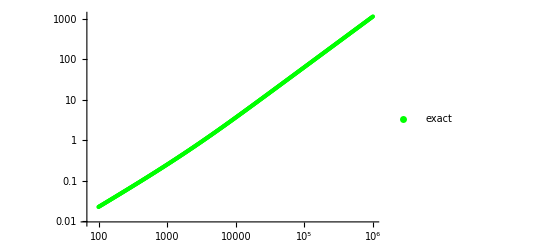

```mathematica
P0 =ListLogLogPlot[{Exp[#[[1]]], Exp[#[[1]]-#[[2]]]}&/@edectab[[500;;]],
PlotLegends->{"exact"}, PlotStyle->{Green}]
```

```mathematica
|
```

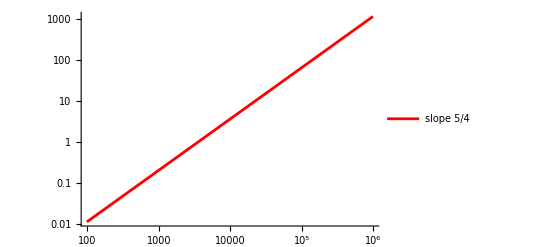

```mathematica
P1 =Block[{ x0, y0, x1, a},
a = edectab[[500]][[1]];
{x0,y0} = edectab[[-200]];
x1 = edectab[[-1]][[1]];
LogLogPlot[Exp[x0-y0] (x/Exp[x0])^(5/4),{x,Exp[a],Exp[x1]}, 
PlotLegends->{"slope 5/4"}, PlotStyle->{Red, Tiny}]
]
```

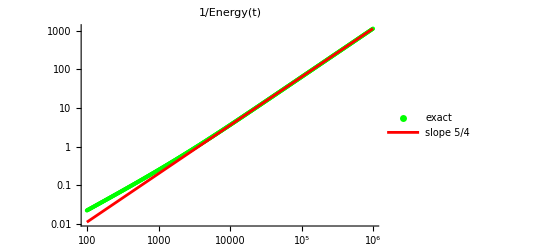

```mathematica
Show[{P0, P1}, PlotRange->All,PlotLabel->"1/Energy(t)"]
```

```mathematica
EDis[1]
```

4499.65

```mathematica
EDec[1]
```

4498.65

```mathematica
ne[t_] :=  EDis[t]/EDec[t]/t;
```

```mathematica
netable[k0_, k1_, M_] :=  
ParallelTable[Block[{k},
k = N[k0 (k1/k0)^(n/M )];
{Log[k^2], ne[k^2]}]
,{n,0,M}];
```

```mathematica
ntab = netable[0.1, 1000,1000];
```

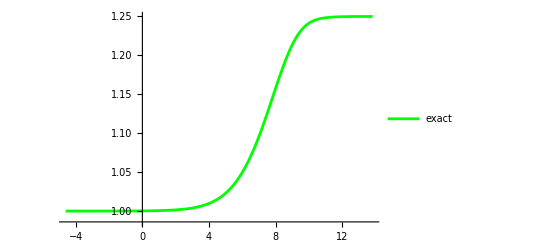

```mathematica
Pe1 =ListLinePlot[ntab, PlotStyle->Green, PlotLegends->{"exact"}]
```

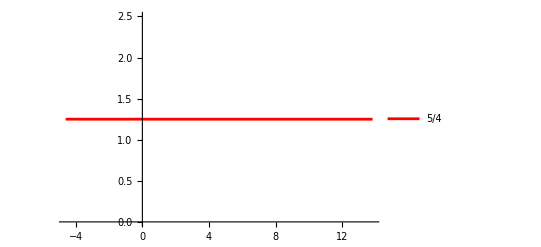

```mathematica
Pe2 = Plot[5/4,{x,2 Log[0.1], 2 Log[1000]}, PlotStyle->Red, PlotLegends->{"5/4"}]
```

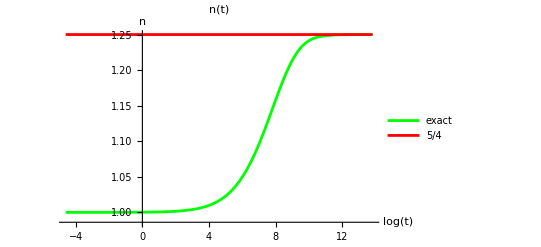

```mathematica
Show[{Pe1, Pe2}, PlotLabel->"n(t)", AxesLabel->{Log[t], n}]
```

```mathematica
(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]q(q+1))
```

```mathematica
FunctionPoles[(Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]q(q+1)),p]//TableForm
```

-17/2 | 1
-13/2 | 1
-7/2 | 1
ConditionalExpression[1/2 (-17-4 C[1]), C[1]∈ℤ&&C[1]≥1] | 1
ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1+2 C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1/2 (-17+2 ZetaZero[C[1]]), C[1]∈ℤ] | Indeterminate

```mathematica
Diss =FullSimplify[4 Pi ν/t^2 Integrate[κ^(p+2),{κ,k Sqrt[ ν t],Infinity}, GenerateConditions->False],{t >0, ν >0,p >0}]
```

-(4 k^4 π ν^3 (k √(t ν))^(-1+p))/(3+p)

```mathematica
Edec = Integrate[Diss,{t,t0, Infinity},GenerateConditions->False]
```

(8 k^3 π (1/t0)^(-1/2-p/2) (k √ν)^p ν^(5/2))/(3+4 p+p^2)

```mathematica
FullSimplify[Edec/.{p->2 q -1, t0->1}]
```

(2 k^2 π (k √ν)^(2 q) ν^2)/(q+q^2)

```mathematica
FullSimplify[((Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]q(q+1)))/.p-> 2 q -1]
```

-(2 Gamma[-2 q] Zeta[13/2+2 q])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q])

```mathematica
FunctionPoles[-(2 Gamma[-2 q] Zeta[13/2+2 q])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]),q]//TableForm
```

-15/4 | 1
-11/4 | 1
-5/4 | 1
-1 | 1
ConditionalExpression[1/4 (-15-4 C[1]), C[1]∈ℤ&&C[1]≥1] | 1
ConditionalExpression[C[1], C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1/2 (1+2 C[1]), C[1]∈ℤ&&C[1]≥0] | 1
ConditionalExpression[1/4 (-15+2 ZetaZero[C[1]]), C[1]∈ℤ] | Indeterminate

```mathematica
pts1 =  FunctionPoles[{-(2 Gamma[-2 q] Zeta[13/2+2 q])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]),{ Abs[q] < 40}},q]
```

{{-159/4,1},{-155/4,1},{-151/4,1},{-147/4,1},{-143/4,1},{-139/4,1},{-135/4,1},{-131/4,1},{-127/4,1},{-123/4,1},{-119/4,1},{-115/4,1},{-111/4,1},{-107/4,1},{-103/4,1},{-99/4,1},{-95/4,1},{-91/4,1},{-87/4,1},{-83/4,1},{-79/4,1},{-75/4,1},{-71/4,1},{-67/4,1},{-63/4,1},{-59/4,1},{-55/4,1},{-51/4,1},{-47/4,1},{-43/4,1},{-39/4,1},{-35/4,1},{-31/4,1},{-27/4,1},{-23/4,1},{-19/4,1},{-15/4,1},{-11/4,1},{-5/4,1},{-1,1},{0,1},{1/2,1},{1,1},{3/2,1},{2,1},{5/2,1},{3,1},{7/2,1},{4,1},{9/2,1},{5,1},{11/2,1},{6,1},{13/2,1},{7,1},{15/2,1},{8,1},{17/2,1},{9,1},{19/2,1},{10,1},{21/2,1},{11,1},{23/2,1},{12,1},{25/2,1},{13,1},{27/2,1},{14,1},{29/2,1},{15,1},{31/2,1},{16,1},{33/2,1},{17,1},{35/2,1},{18,1},{37/2,1},{19,1},{39/2,1},{20,1},{41/2,1},{21,1},{43/2,1},{22,1},{45/2,1},{23,1},{47/2,1},{24,1},{49/2,1},{25,1},{51/2,1},{26,1},{53/2,1},{27,1},{55/2,1},{28,1},{57/2,1},{29,1},{59/2,1},{30,1},{61/2,1},{31,1},{63/2,1},{32,1},{65/2,1},{33,1},{67/2,1},{34,1},{69/2,1},{35,1},{71/2,1},{36,1},{73/2,1},{37,1},{75/2,1},{38,1},{77/2,1},{39,1},{79/2,1},{1/4 (-15+2 ZetaZero[-21]),1},{1/4 (-15+2 ZetaZero[-20]),1},{1/4 (-15+2 ZetaZero[-19]),1},{1/4 (-15+2 ZetaZero[-18]),1},{1/4 (-15+2 ZetaZero[-17]),1},{1/4 (-15+2 ZetaZero[-16]),1},{1/4 (-15+2 ZetaZero[-15]),1},{1/4 (-15+2 ZetaZero[-14]),1},{1/4 (-15+2 ZetaZero[-13]),1},{1/4 (-15+2 ZetaZero[-12]),1},{1/4 (-15+2 ZetaZero[-11]),1},{1/4 (-15+2 ZetaZero[-10]),1},{1/4 (-15+2 ZetaZero[-9]),1},{1/4 (-15+2 ZetaZero[-8]),1},{1/4 (-15+2 ZetaZero[-7]),1},{1/4 (-15+2 ZetaZero[-6]),1},{1/4 (-15+2 ZetaZero[-5]),1},{1/4 (-15+2 ZetaZero[-4]),1},{1/4 (-15+2 ZetaZero[-3]),1},{1/4 (-15+2 ZetaZero[-2]),1},{1/4 (-15+2 ZetaZero[-1]),1},{1/4 (-15+2 ZetaZero[1]),1},{1/4 (-15+2 ZetaZero[2]),1},{1/4 (-15+2 ZetaZero[3]),1},{1/4 (-15+2 ZetaZero[4]),1},{1/4 (-15+2 ZetaZero[5]),1},{1/4 (-15+2 ZetaZero[6]),1},{1/4 (-15+2 ZetaZero[7]),1},{1/4 (-15+2 ZetaZero[8]),1},{1/4 (-15+2 ZetaZero[9]),1},{1/4 (-15+2 ZetaZero[10]),1},{1/4 (-15+2 ZetaZero[11]),1},{1/4 (-15+2 ZetaZero[12]),1},{1/4 (-15+2 ZetaZero[13]),1},{1/4 (-15+2 ZetaZero[14]),1},{1/4 (-15+2 ZetaZero[15]),1},{1/4 (-15+2 ZetaZero[16]),1},{1/4 (-15+2 ZetaZero[17]),1},{1/4 (-15+2 ZetaZero[18]),1},{1/4 (-15+2 ZetaZero[19]),1},{1/4 (-15+2 ZetaZero[20]),1},{1/4 (-15+2 ZetaZero[21]),1}}

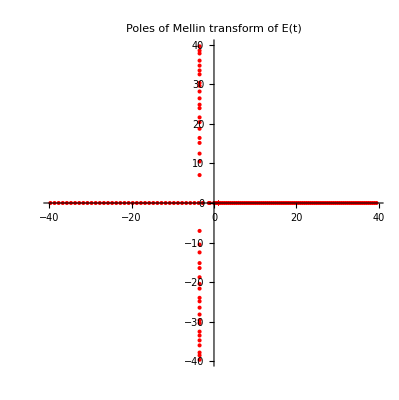

```mathematica
ComplexListPlot[pts1, PlotStyle->{Red},PlotLabel->"Poles of Mellin transform of E(t)"]
```

```mathematica
FullSimplify[Integrate[4 Pi  κ^p Sin[ κ ρ]/ ((2 Pi)^3(κ ρ)),{κ, 0, Infinity},GenerateConditions->False]/.p->-p-1,{ ρ>0, p >0}]
```

-(ρ^p Cos[(p π)/2] Gamma[-1-p])/(2 π^2)

```mathematica
FullSimplify[-Cos[(p π)/2] Gamma[-1-p]((Gamma[-p] Zeta[15/2+p])/((7+2 p) (17+2 p) Zeta[17/2+p]))/.p->-p-1]
```

(Gamma[p] Gamma[1+p] Sin[(p π)/2] Zeta[13/2-p])/((75+4 (-10+p) p) Zeta[15/2-p])

```mathematica
Factor[(75+4 (-10+p) p)]
```

(-15+2 p) (-5+2 p)

```mathematica
FunctionPoles[(Gamma[p] Gamma[1+p] Sin[(p π)/2] Zeta[13/2-p])/((-15+2 p) (-5+2 p) Zeta[15/2-p]),p]//TableForm
```

5/2 | 1
11/2 | 1
15/2 | 1
ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≤0] | Indeterminate
ConditionalExpression[-1+2 C[1], C[1]∈ℤ&&C[1]≤0] | 2
ConditionalExpression[1+2 C[1], C[1]∈ℤ&&C[1]≤-1] | 2
ConditionalExpression[1/2 (15+4 C[1]), C[1]∈ℤ&&C[1]≥1] | 1
ConditionalExpression[1/2 (15-2 ZetaZero[C[1]]), C[1]∈ℤ] | Indeterminate

```mathematica
pts2 = FunctionPoles[{-(Gamma[p] Gamma[1+p] Sin[(p π)/2] Zeta[13/2-p])/((-15+2 p) (-5+2 p) Zeta[15/2-p]),{0 < Re[p] <30, Im[p]==0}},p]
```

{{5/2,1},{11/2,1},{15/2,1},{19/2,1},{23/2,1},{27/2,1},{31/2,1},{35/2,1},{39/2,1},{43/2,1},{47/2,1},{51/2,1},{55/2,1},{59/2,1}}

```mathematica
pts3 = FunctionPoles[{-(Gamma[p] Gamma[1+p] Sin[(p π)/2] Zeta[13/2-p])/((-15+2 p) (-5+2 p) Zeta[15/2-p]),{6.5 <Re[p]< 7.5, Abs[Im[p]]< 30}},p]
```

{{7.+25.0109 ⅈ,1},{7.+21.022 ⅈ,1},{7.+14.1347 ⅈ,1},{7.-14.1347 ⅈ,1},{7.-21.022 ⅈ,1},{7.-25.0109 ⅈ,1}}

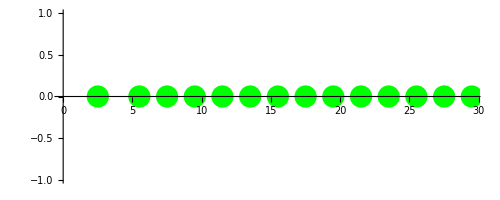

```mathematica
RP =ComplexListPlot[#[[1]]&/@pts2, PlotStyle->{Green,PointSize[0.04]}]
```

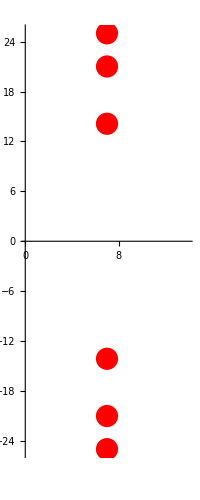

```mathematica
IP = ComplexListPlot[#[[1]]&/@pts3, PlotStyle->{Red, PointSize[0.04]}]
```

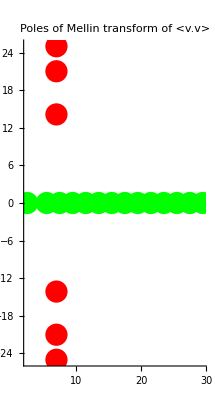

```mathematica
Show[{RP,IP},PlotLabel->"Poles of Mellin transform of <v.v>", PlotRange->All]
```

```mathematica
Series[(Gamma[p] Gamma[1+p] Sin[(p π)/2] Zeta[13/2-p])/((-15+2 p) (-5+2 p) Zeta[15/2-p]),{p,-1,0}]
```

Zeta[15/2]/(119 Zeta[17/2] (p+1)^2)+(167 Zeta[15/2] Zeta[17/2]-238 EulerGamma Zeta[15/2] Zeta[17/2]-119 Zeta[17/2] Zeta'[15/2]+119 Zeta[15/2] Zeta'[17/2])/(14161 Zeta[17/2]^2 (p+1))+1/(40443816 Zeta[17/2]^3)(520824 Zeta[15/2] Zeta[17/2]^2-953904 EulerGamma Zeta[15/2] Zeta[17/2]^2+679728 EulerGamma^2 Zeta[15/2] Zeta[17/2]^2+14161 π^2 Zeta[15/2] Zeta[17/2]^2-476952 Zeta[17/2]^2 Zeta'[15/2]+679728 EulerGamma Zeta[17/2]^2 Zeta'[15/2]+476952 Zeta[15/2] Zeta[17/2] Zeta'[17/2]-679728 EulerGamma Zeta[15/2] Zeta[17/2] Zeta'[17/2]-339864 Zeta[17/2] Zeta'[15/2] Zeta'[17/2]+339864 Zeta[15/2] Zeta'[17/2]^2+169932 Zeta[17/2]^2 Zeta''[15/2]-169932 Zeta[15/2] Zeta[17/2] Zeta''[17/2])+O[p+1]^1

```mathematica
{{5/2, 1}, {11/2, 1}, {15/2, 1}, {ConditionalExpression[2 C[1], C[1]∈Integers&&C[1]<0], 1}, {ConditionalExpression[-1+2 C[1], C[1]∈Integers&&C[1]≤0], 2}, {ConditionalExpression[1/2 (15+4 C[1]), C[1]∈Integers&&C[1]≥1], 1}, {ConditionalExpression[1/2 (15-2 ZetaZero[C[1]]), C[1]∈Integers], Indeterminate}}
```

```mathematica
ee[q_] := -(2 Gamma[-2 q] Zeta[13/2+2 q]f[2 q -1])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q])
```

```mathematica
Residue[ -(2 Gamma[-2 q] Zeta[13/2+2 q]f[2 q -1])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]), {q,-5/4}]
```

(π^(9/2) f[-7/2])/(600 Zeta[5])

```mathematica
Residue[ -(2 Gamma[-2 q] Zeta[13/2+2 q]f[2 q -1])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]), {q,-11/4}]/Residue[ -(2 Gamma[-2 q] Zeta[13/2+2 q]f[2 q -1])/((1+q) (5+4 q) (15+4 q) Zeta[15/2+2 q]), {q,-5/4}]
```

-(10125 f[-13/2] Zeta[5])/(4 π^6 f[-7/2])

```mathematica
ABC[0.26]
```

{1.1474,0.00270802,0.0588501}

```mathematica
ff[q_]:=
Block[{ tab,OKtab, interp, delta = (Δ2 - Δ1)/1000, p = 2 q-1},
tab =(*Parallel*)Table[
Block[{A,B,C,F} ,
{A,B,C}= ABC[Δ];
(*Print[{Δ,{A,B,C}}];*)
F = 20 C^(p-1) (A C - B p);
{Δ,Log[F]}], {Δ,Δ1, Δ2, delta}];
OKtab = Select[tab,NumericQ[#[[2]]]&];
If[Length[OKtab] < 10, Return[None]];
interp = Interpolation[OKtab,InterpolationOrder->5];
NIntegrate[(1-Δ)Exp[interp[Δ]],{Δ,Δ1, Δ2}]
]
```

```mathematica
ff[-13/2]
```

1.25058×10^18

```mathematica
ff[-7/2]
```

4.09069×10^10

```mathematica
-(10125 1.2505787852221153*^18 Zeta[5])/(4 π^6 4.09068904781942*^10)
```

-8.34639×10^7

```mathematica
N[10/7]
```

1.42857

```mathematica
tdata = Flatten[ToExpression /@Import["Decaying_turbulence/k2_rega/case2.1_t.txt","Table"]];
```

```mathematica
Dimensions[tdata]
```

{2147}

```mathematica
Edata = Flatten [ToExpression /@Import["Decaying_turbulence/k2_rega/case2.1_tke.txt","Table"]];
```

```mathematica
Dimensions[Edata]
```

{2147}

```mathematica
Edata[[1]]
```

0.745992

```mathematica
tdata[[1]]
```

0.

```mathematica
tedata = Transpose[{tdata,Edata}];
```

```mathematica
tedata[[1]]
```

{0.,0.745992}

```mathematica
tedata[[-1]]
```

{125.,0.00015362}

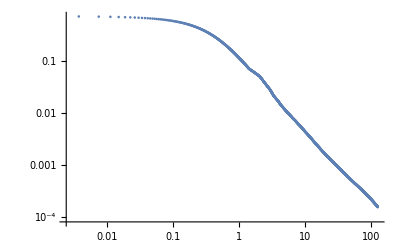

```mathematica
ListLogLogPlot[tedata]
```

```mathematica
energyDecayTab = {Exp[#[[1]]], Exp[#[[2]]-#[[1]]]}&/@edectab;
```

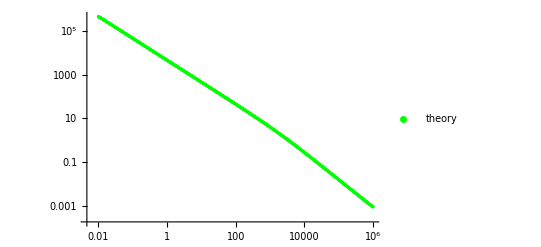

```mathematica
ListLogLogPlot[energyDecayTab,
PlotLegends->{"theory"}, PlotStyle->{Green}]
```

```mathematica
ltedata = Log[tedata[[2;;]]];
```

```mathematica
ltedata[[1]]
```

{-5.57275,-0.301589}

```mathematica
ltedata[[-1]]
```

{4.82831,-8.78103}

```mathematica
lteinterp = Interpolation[ltedata]
```

InterpolatingFunction[…]

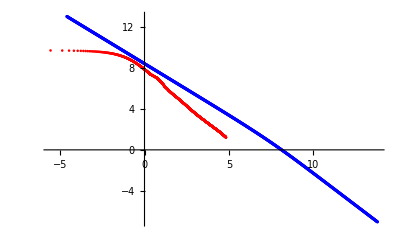

```mathematica
Show[{ ListPlot[{#[[1]], 10 +#[[2]]}& /@ltedata, PlotStyle->Red],ListLogLogPlot[energyDecayTab, PlotStyle->Blue]}, PlotRange->All]
```

```mathematica
a =.; t0 = .;
```

```mathematica
nlm =NonlinearModelFit[ltedata[[-1000;;]],a - 5/4 Log[Exp[l] + t0],{a, t0},l]
```

FittedModel[-2.70753-5/4 Log[«1»]]

```mathematica
nlm["ParameterTable"]
```

General::munfl: Exp[-4680.84] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -2.70753 | 0.000790115 | -3426.75 | 0.
t0 | -0.47367 | 0.0203582 | -23.2667 | 5.18043×10^-96

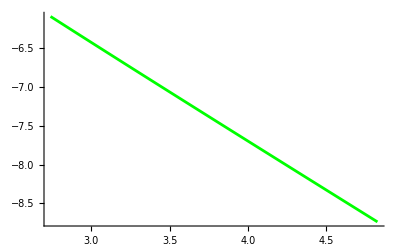

```mathematica
P2 = Plot[nlm[l],{l,ltedata[[-1000,1]], ltedata[[-1,1]]}, PlotStyle->Green]
```

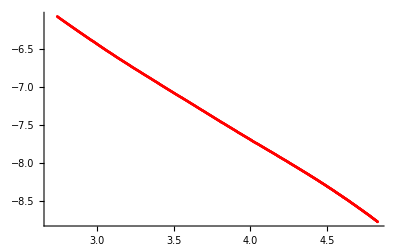

```mathematica
P1 = ListPlot[ltedata[[-1000;;]], PlotStyle->Red]
```

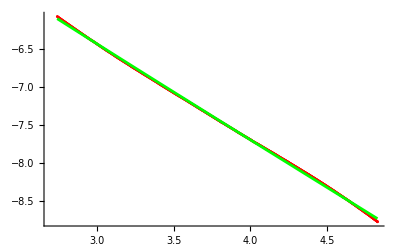

```mathematica
Show[{P1, P2}]
```

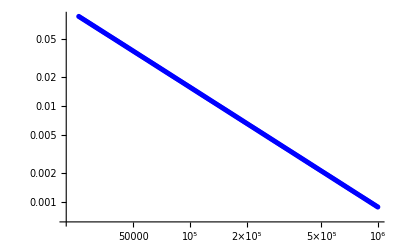

```mathematica
P3 = ListLogLogPlot[energyDecayTab[[-200;;]], PlotStyle->Blue]
```

```mathematica
p =.; t1=.;
```

```mathematica
lentab = Log[energyDecayTab];
```

```mathematica
nlm2 = NonlinearModelFit[lentab[[-200;;]],p - 5/4 l,{p},l]
```

FittedModel[10.2398-(5 l)/4]

```mathematica
nlm2["ParameterTable"]
```

General::munfl: Exp[-1848.24] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
p | 10.2398 | 0.0000681674 | 150215. | 0.

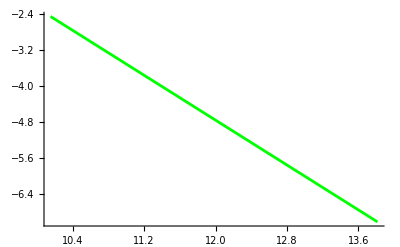

```mathematica
P4 = Plot[nlm2[l],{l,lentab[[-200,1]], lentab[[-1,1]]}, PlotStyle->Green]
```

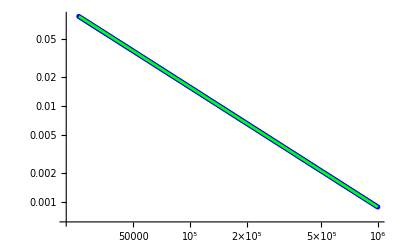

```mathematica
Show[{P3, P4}]
```

```mathematica
a=.; b= .; t0 = .;
```

```mathematica
nlm3 =NonlinearModelFit[ltedata[[-1000;;]],a + nlm2[Log[b Exp[l]+ t0]],{a,b, t0},l]
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

FittedModel[1.81349-5/4 Log[-«19»+«19» ⅇ^l]]

```mathematica
nlm3["ParameterTable"]
```

General::munfl: Exp[-3228.12] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1421.4] is too small to represent as a normalized machine number; precision may be lost.

| Estimate | Standard Error | t-Statistic | P-Value
a | -8.42629 | 0.0105209 | -800.907 | 0.
b | 37.2187 | 0.292993 | 127.029 | 0.
t0 | -17.6294 | 0.619305 | -28.4664 | 6.19226×10^-131

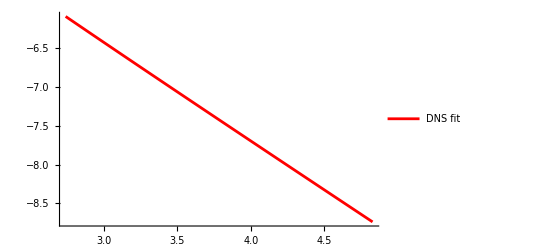

```mathematica
P5 =Plot[nlm3[l],{l, ltedata[[-1000,1]],ltedata[[-1,1]]},
 PlotStyle->Red, PlotLegends->{ "DNS fit"}]
```

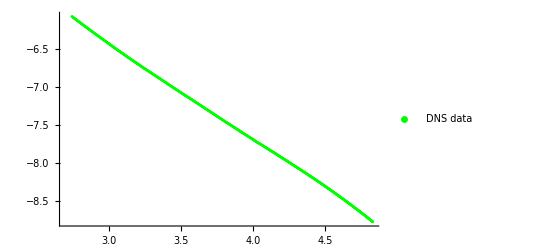

```mathematica
P6 = ListPlot[ltedata[[-1000;;]],PlotStyle->Green,PlotLegends->{ "DNS data"}]
```

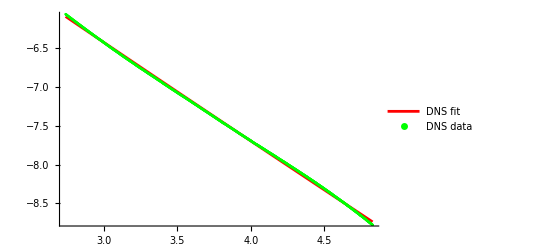

```mathematica
Show[{P5,P6}]
```

```mathematica
enInterp = Interpolation[lentab];
```

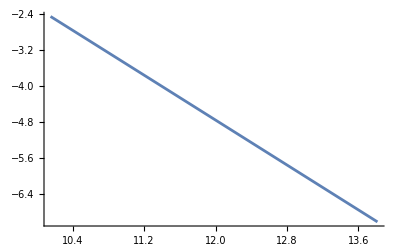

```mathematica
Plot[enInterp[l],{l, lentab[[-200,1]], lentab[[-1,1]]}]
```